# A mathematical model for universal semantics (Text mining in Polish)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Polish translation of Jane Austen’s Pride and Prejudice is freely available from http://www.rulit.me/books/duma-i-uprzedzenie-read-270058-1.html

After manual cleansing, we save the text as Duma i uprzedzenie.txt,  which begins with

I
Jest prawdą powszechnie znaną, że samotnemu a bogatemu mężczyźnie brak do
szczęścia tylko żony. Jakkolwiek za pojawieniem się takiego pana w sąsiedztwie niewiele
wiadomo o jego poglądach czy uczucia

and ends with

rdecznych stosunkach. Darcy, tak
jak i Elżbieta szczerze ich kochał, oboje zaś zachowali na zawsze gorącą wdzięczność dla
tych, którzy przywożąc Elżbietę do hrabstwa Derby, pozwolili im się połączyć.

The current Mathematica Notebook demonstrates the analysis of Pride and Prejudice. For the analysis of other texts in our current work, one needs to download text corpora and modify the codes slightly.

### Origin of Species

The full text  for a Polish translation of Charles Darwin’s Origin of Species is freely available from https://wolnelektury.pl/katalog/lektura/darwin-o-powstawaniu-gatunkow/

After manual cleansing, the text begins with

Rozdział I.
Przemiany w stanie udomowienia

Przyczyny zmienności. — Wpływ przyzwyczajenia oraz używania lub nieużywania narządów. — Zmienność współzależna. — Dziedziczność. — Cechy odmian hodowlanych.

and ends with

gając ścisłym prawom ciążenia, dokonywała swych obrotów, z tak prostego początku zdołał się rozwinąć i wciąż jeszcze się rozwija nieskończony szereg form najpiękniejszych i najbardziej zadziwiających.

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Polish

Our major resources for the Polish language are:

Iwona Sadowska, Polish: A Comprehensive Grammar, Routledge, Oxford, UK, 2012

Wiktionary (English and Polish)

Wolne Lektury (wolnelektury.pl)

## Polish case conversions

As of v10.4, Mathematica does not have built-in support for lower- and upper-case conversions of special Polish letters.

```mathematica
Alphabet["Polish"]
```

{a,ą,b,c,ć,d,e,ę,f,g,h,i,j,k,l,ł,m,n,ń,o,ó,p,r,s,ś,t,u,w,y,z,ź,ż}

```mathematica
StringMatchQ[#,LetterCharacter]&/@%
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
ToUpperCase[%%]
```

{A,Ą,B,C,Ć,D,E,Ę,F,G,H,I,J,K,L,Ł,M,N,Ń,O,Ó,P,R,S,Ś,T,U,W,Y,Z,Ź,Ż}

```mathematica
PolishToUpperCase[s_]:=StringReplace[ToUpperCase[s],{"ą":>"Ą","ę":> "Ę","ń":> "Ń","ś":>"Ś","ź":> "Ź","ż":>"Ż" }]
```

```mathematica
PolishToLowerCase[s_]:=StringReplace[ToLowerCase[s],{"Ą":>"ą","Ę":>"ę","Ń":>"ń","Ś":>"ś","Ź":>"ź","Ż":>"ż" }]
```

## Polish stop words

We first extract the Polish stop word list from the following web page:

https://pl.wikipedia.org/wiki/Wikipedia:Stopwords

```mathematica
PolishStopWords0={"a","aby","ach","acz","aczkolwiek","aj","albo","ale","ależ","ani","aż","bardziej","bardzo","bo","bowiem","by","byli","bynajmniej","być","był","była","było","były","będzie","będą","cali","cała","cały","ci","cię","ciebie","co","cokolwiek","coś","czasami","czasem","czemu","czy","czyli","daleko","dla","dlaczego","dlatego","do","dobrze","dokąd","dość","dużo","dwa","dwaj","dwie","dwoje","dziś","dzisiaj","gdy","gdyby","gdyż","gdzie","gdziekolwiek","gdzieś","i","ich","ile","im","inna","inne","inny","innych","iż","ja","ją","jak","jakaś","jakby","jaki","jakichś","jakie","jakiś","jakiż","jakkolwiek","jako","jakoś","je","jeden","jedna","jedno","jednak","jednakże","jego","jej","jemu","jest","jestem","jeszcze","jeśli","jeżeli","już","ją","każdy","kiedy","kilka","kimś","kto","ktokolwiek","ktoś","która","które","którego","której","który","których","którym","którzy","ku","lat","lecz","lub","ma","mają","mało","mam","mi","mimo","między","mną","mnie","mogą","moi","moim","moja","moje","może","możliwe","można","mój","mu","musi","my","na","nad","nam","nami","nas","nasi","nasz","nasza","nasze","naszego","naszych","natomiast","natychmiast","nawet","nią","nic","nich","nie","niech","niego","niej","niemu","nigdy","nim","nimi","niż","no","o","obok","od","około","on","ona","one","oni","ono","oraz","oto","owszem","pan","pana","pani","po","pod","podczas","pomimo","ponad","ponieważ","powinien","powinna","powinni","powinno","poza","prawie","przecież","przed","przede","przedtem","przez","przy","roku","również","sama","są","się","skąd","sobie","sobą","sposób","swoje","ta","tak","taka","taki","takie","także","tam","te","tego","tej","temu","ten","teraz","też","to","tobą","tobie","toteż","trzeba","tu","tutaj","twoi","twoim","twoja","twoje","twym","twój","ty","tych","tylko","tym","u","w","wam","wami","was","wasz","wasza","wasze","we","według","wiele","wielu","więc","więcej","wszyscy","wszystkich","wszystkie","wszystkim","wszystko","wtedy","wy","właśnie","z","za","zapewne","zawsze","ze","zł","znowu","znów","został","żaden","żadna","żadne","żadnych","że","żeby"};
```

We then add inflected forms of pronouns.

```mathematica
PolishStopWords1={"ci","cię","ciebie","co","czego","czemu","czym","go","ich","im","ją","ja","je","jego","jej","jemu","kim","kogo","komu","kto","mi","mię","mną","mnie","mu","my","nam","nami","nas","nią","nic","nich","niczego","niczemu","niczym","niej","nikim","nikogo","nikomu","nikt","nim","nimi","on","ona","one","oni","ono","tobą","tobie","ty","wami","was","wy","kogoś","komuś","kimś","czegoś","czemuś","czymś"}∪{"każdą","każda","każde","każdego","każdej","każdemu","każdy","każdych","każdym","każdymi"}∪{"wszyscy","wszystkich","wszystkim","wszystkimi"}∪{"wszystkich","wszystkie","wszystkim","wszystkimi"}∪{"wszyscy","wszystek","wszystką","wszystka","wszystkich","wszystkie","wszystkiego","wszystkiej","wszystkiemu","wszystkim","wszystkimi","wszystko"}∪{"wszystkiego","wszystkiemu","wszystkim","wszystko"}∪{"móc","może","możecie","możemy","możesz","mogą","mogę","mogąc","mogąca","mogące","mogący","mógł","mogła","mogłaś","mogłaby","mogłabyś","mogłabym","mogłam","mógłby","mógłbyś","mógłbym","mogłeś","mogłem","mogli","mogliby","moglibyście","moglibyśmy","mogliście","mogliśmy","mogło","mogłoś","mogłoby","mogłobyś","mogłobym","mogłom","mogły","mogłyby","mogłybyście","mogłybyśmy","mogłyście","mogłyśmy"}∪{"zbyt"}∪{"sam","samą","sama","same","samego","samej","samemu","sami","samo","samych","samym","samymi"}∪{"jacy","jaką","jaka","jaki","jakich","jakie","jakiego","jakiej","jakiemu","jakim","jakimi"}∪{"ma","macie","mają","mając","mająca","mające","mający","mam","mamy","masz","miał","miał1","miała","miałaś","miałaby","miałabyś","miałabym","miałam","miałby","miałbyś","miałbym","miałeś","miałem","miało","miałoby","miały","miałyby","miałybyście","miałybyśmy","miałyście","miałyśmy","miano","mieć","miej","miejcie","miejmy","mieli","mieliby","mielibyście","mielibyśmy","mieliście","mieliśmy"}∪{"którą","która","które","którego","której","któremu","który","których","którym","którymi","którzy"}∪{"jeden","jedną","jedna","jedne","jednego","jednej","jednemu","jedni","jedno","jednych","jednym","jednymi"}∪{"oba","obaj","obie","obiema","oboje","obojga","obojgiem","obojgu","oboma","obu"}∪{"często"}∪{"choć","choćby","chociaż"}∪{"bym","byś","by","byśmy","byście"}∪{"bądź","będą","będę","będąc","będąca","będące","bądźcie","będący","bądźmy","będzie","będziecie","będziemy","będziesz","być","bycie","był","była","byłaś","byłaby","byłabyś","byłabym","byłam","byłby","byłbyś","byłbym","byłeś","byłem","byli","byliby","bylibyście","bylibyśmy","byliście","byliśmy","było","byłoby","były","byłyby","byłybyście","byłybyśmy","byłyście","byłyśmy","bywszy","jest","jesteś","jesteście","jestem","jesteśmy","są"}∪{"razem"}∪{"doń","nań"}∪{"mą","me","mego","mej","memu","moich","moimi","moją","mojego","mojej","mojemu","mych","mym","mymi"}∪{"naszą","naszej","naszemu","naszym","naszymi"}∪{"twą","twa","twe","twego","twej","twemu","twoich","twoimi","twoją","twojego","twojej","twojemu","twych","twymi"}∪{"wasi","waszą","waszego","waszej","waszemu","waszych","waszym","waszymi"}∪{"swą","swa","swe","swego","swej","swemu","swoi","swoich","swoim","swoimi","swój","swoją","swoja","swojego","swojej","swojemu","swych","swym","swymi"}∪{"tą","tę","tamci","tamtą","tamta","tamte","tamtego","tamtej","tamtemu","tamten","tamto","tamtych","tamtym","tamtymi","tymi"}∪{"jacy"}∪{"jacyś","jakąś","jakieś","jakiegoś","jakiejś","jakiemuś","jakimś","jakimiś"}∪{"czegokolwiek","czemukolwiek","czymkolwiek","kimkolwiek","kogokolwiek","komukolwiek"}∪{"niektóre","niektórych","niektórym","niektórymi","niektórzy"}∪{"siebie"}∪{"powinieneś","powinienem","powinnaś","powinnam","powinniście","powinniśmy","powinny","powinnyście","powinnyśmy"}∪{"nieco"}∪{"bez"}∪{"inną","inna","inne","innego","innej","innemu","inni","inny","innych","innym","innymi"}∪{"tyle","tyloma","tylu"}∪{"ile","iloma","ilu"}∪{"musi","musiał","musiała","musiałaś","musiałaby","musiałabyś","musiałabym","musiałam","musiałby","musiałbyś","musiałbym","musiałeś","musiałem","musiało","musiałoś","musiałoby","musiałobyś","musiałobym","musiałom","musiały","musiałyby","musiałybyście","musiałybyśmy","musiałyście","musiałyśmy","musicie","musieć","musieli","musieliby","musielibyście","musielibyśmy","musieliście","musieliśmy","musimy","musisz","muszą","muszę","musząc","musząca","muszące","muszący"}∪{"niechaj"}∪{"oby","obym","obyś","obyśmy","obyście"}∪{"skoro","albowiem","dopóki"}∪{"koło","oprócz","wśród","dzięki","przeciw","przeciwko","wbrew","poprzez","pomiędzy","zza","naokoło","spomiędzy","spośród","sponad","spoza","dosyć"}∪{"tacy","taką","taka","taki","takich","takie","takiego","takiej","takiemu","takim","takimi"}∪{"najbardziej"}∪{"inną","inna","inne","innego","innej","innemu","inni","inny","innych","innym","innymi"}∪{"cóż","chyba"}∪{"ów","ową","owa","owe","owego","owej","owemu","owi","owo","owych","owym","owymi"}∪{"wobec","naprzeciw","przed","zaś","natomiast","znowu","potem","później","zaraz"}∪{"czyż","czyżby","czyżbym","czyżbyś","czyżbyśmy","czyżbyście"}∪{"gdybym","gdybyś","gdybyśmy","gdybyście"}∪{"ż","coraz"}∪{"jeden","jedną","jedna","jedne","jednego","jednej","jednemu","jedni","jedno","jednych","jednym","jednymi","jedyną","jedyna","jedyne","jedynego","jedynej","jedynemu","jedyni","jedynie","jedyny","jedynych","jedynym","jedynymi"}∪{"wszak","wszakże"}∪{"czyjś","dokądś","ileś","kiedyś","któryś","skądś","tyś","doprawdy","wkrótce"}∪{"wielu","wiele","wieloma"};
```

```mathematica
PolishStopWords=PolishStopWords0∪PolishStopWords1;
```

## Polish sample words

At the time of writing (June 2016), the English version of Wiktionary (http://en.wiktionary.org) does not contain completely classified grammatical tables for the Polish language, so we have to refer to the Polish version of Wiktionary (https://pl.wiktionary.org/wiki/Kategoria:Gramatyka_j%C4%99zyka_polskiego) instead, for the divisions of declension and conjugation classes, of nouns and verbs respectively. For the declension types of adjectives, we follow §4.7 in Iwona Sadowska’s aforementioned grammar book.

Consonants at the end of a Polish word stem are subject to change during inflections. Vowel alternations are also possible.

```mathematica
gorillaPolish={"goryl","goryla","gorylach","gorylami","goryle","gorylem","goryli","gorylom","gorylowi","gorylu"};
```

```mathematica
leafPolish={"liść","liści","liścia","liściach","liście","liściem","liściom","liściowi","liściu","liśćmi"};
```

```mathematica
rascalPolish={"drań","drani","drania","draniach","draniami","dranie","draniem","draniom","draniów","draniowi","draniu"};
```

```mathematica
PolishNounMasc1=gorillaPolish∪leafPolish∪rascalPolish;
```

```mathematica
tapewormPolish={"tasiemca","tasiemcach","tasiemcami","tasiemce","tasiemcem","tasiemcom","tasiemców","tasiemcowi","tasiemcu","tasiemiec"};
```

```mathematica
fruitPolish={"owoc","owocach","owocami","owoce","owocem","owocom","owoców","owocowi","owocu"};
```

```mathematica
guardPolish={"stróż","stróża","stróżach","stróżami","stróżem","stróżom","stróżowi","stróżowie","stróżu","stróży"};
```

```mathematica
PolishNounMasc2=tapewormPolish∪fruitPolish∪guardPolish;
```

```mathematica
firemanPolish={"strażacy","strażak","strażaka","strażakach","strażakami","strażakiem","strażakom","strażaków","strażakowi","strażaku"};
```

```mathematica
surgeonPolish={"chirurdzy","chirurg","chirurga","chirurgach","chirurgami","chirurgiem","chirurgom","chirurgów","chirurgowi","chirurgu"};
```

```mathematica
sheepskinPolish={"kożuch","kożucha","kożuchach","kożuchami","kożuchem","kożuchom","kożuchów","kożuchowi","kożuchu","kożuchy"};
```

```mathematica
PolishNounMasc3=firemanPolish∪surgeonPolish∪sheepskinPolish;
```

```mathematica
thrushPolish={"droździe","drozd","drozda","drozdach","drozdami","drozdem","drozdom","drozdów","drozdowi","drozdy"};
```

```mathematica
breadPolish={"chleb","chleba","chlebach","chlebami","chlebem","chlebie","chlebom","chlebów","chlebowi","chleby"};
```

```mathematica
doctorPolish={"doktor","doktora","doktorach","doktorami","doktorem","doktorom","doktorów","doktorowi","doktorowie","doktorze","doktorzy"};
```

```mathematica
PolishNounMasc4=thrushPolish∪breadPolish∪doctorPolish;
```

```mathematica
MartianPolish={"Marsjan","Marsjanach","Marsjanami","Marsjanie","Marsjanin","Marsjanina","Marsjaninem","Marsjaninie","Marsjaninowi","Marsjanom","Marsjany"};
```

```mathematica
PolishNounMasc5=MartianPolish;
```

```mathematica
PolishSampleNounsMasc=PolishNounMasc1∪PolishNounMasc2∪PolishNounMasc3∪PolishNounMasc4∪PolishNounMasc5;
```

```mathematica
fieldPolish={"pól","pola","polach","polami","pole","polem","polom","polu"};
```

```mathematica
studioPolish={"studia","studiach","studiami","studiem","studio","studiom","studiów","studiu"};
```

```mathematica
PolishNounNeut1=fieldPolish∪studioPolish;
```

```mathematica
lungPolish={"płuc","płuca","płucach","płucami","płucem","płuco","płucom","płucu"};
```

```mathematica
PolishNounNeut2=lungPolish;
```

```mathematica
overcoatPolish={"palcie","palt","palta","paltach","paltami","paltem","palto","paltom","paltu"};
```

```mathematica
wonderPolish={"cuda","cudach","cudami","cudem","cudo","cudom","cudów","cudu","cudzie"};
```

```mathematica
PolishNounNeut3=overcoatPolish∪wonderPolish;
```

```mathematica
girlPolish={"dziewczę","dziewczęcia","dziewczęciem","dziewczęciu","dziewcząt","dziewczęta","dziewczętach","dziewczętami","dziewczętom"};
```

```mathematica
PolishNounNeut4=girlPolish;
```

```mathematica
shoulderPolish={"ramię","ramienia","ramieniem","ramieniu","ramion","ramiona","ramionach","ramionami","ramionom"};
```

```mathematica
PolishNounNeut5=shoulderPolish;
```

```mathematica
museumPolish={"muzea","muzeach","muzeami","muzeom","muzeów","muzeum"};
```

```mathematica
PolishNounNeut6=museumPolish;
```

```mathematica
PolishSampleNounsNeut=PolishNounNeut1∪PolishNounNeut2∪PolishNounNeut3∪PolishNounNeut4∪PolishNounNeut5∪PolishNounNeut6;
```

```mathematica
pigPolish={"świń","świni","świnią","świnię","świnia","świniach","świniami","świnie","świnio","świniom"};
```

```mathematica
ladyPolish={"pań","pani","panią","paniach","paniami","panie","paniom"};
```

```mathematica
PolishNounFem1=pigPolish∪ladyPolish;
```

```mathematica
jobPolish={"prac","pracą","pracę","praca","pracach","pracami","prace","praco","pracom","pracy"};
```

```mathematica
sootPolish={"sadzą","sadzę","sadza","sadzach","sadzami","sadze","sadzo","sadzom","sadzy"};
```

```mathematica
PolishNounFem2=jobPolish∪sootPolish;
```

```mathematica
rumourPolish={"plotce","plotek","plotką","plotkę","plotka","plotkach","plotkami","plotki","plotko","plotkom"};
```

```mathematica
bowtiePolish={"much","muchą","muchę","mucha","muchach","muchami","mucho","muchom","muchy","musze"};
```

```mathematica
PolishNounFem3=rumourPolish∪bowtiePolish;
```

```mathematica
shapePolish={"form","formą","formę","forma","formach","formami","formie","formo","formom","formy"};
```

```mathematica
PolishNounFem4=shapePolish;
```

```mathematica
eyebrowPolish={"brew","brwi","brwią","brwiach","brwiami","brwiom"};
```

```mathematica
railPolish={"kolei","kolej","koleją","kolejach","kolejami","koleje","kolejom"};
```

```mathematica
bonePolish={"kość","kości","kością","kościach","kościom","kośćmi"};
```

```mathematica
PolishNounFem5=eyebrowPolish∪railPolish∪bonePolish;
```

```mathematica
marePolish={"klacz","klaczą","klaczach","klaczami","klacze","klaczom","klaczy"};
```

```mathematica
mousePolish={"mysz","myszą","myszach","myszami","myszom","myszy"};
```

```mathematica
PolishNounFem6=marePolish∪mousePolish;
```

```mathematica
PolishSampleNounsFem=PolishNounFem1∪PolishNounFem2∪PolishNounFem3∪PolishNounFem4∪PolishNounFem5∪PolishNounFem6;
```

```mathematica
PolishSampleNouns=PolishSampleNounsMasc∪PolishSampleNounsNeut∪PolishSampleNounsFem;
```

```mathematica
goodPolish={"dobrą","dobra","dobre","dobrego","dobrej","dobremu","dobry","dobrych","dobrym","dobrymi","dobrzy"};
```

```mathematica
newPolish={"nową","nowa","nowe","nowego","nowej","nowemu","nowi","nowy","nowych","nowym","nowymi"};
```

```mathematica
tallPolish={"wysocy","wysoką","wysoka","wysoki","wysokich","wysokie","wysokiego","wysokiej","wysokiemu","wysokim","wysokimi"};
```

```mathematica
cheapPolish={"tani","tanią","tania","tanich","tanie","taniego","taniej","taniemu","tanim","tanimi"};
```

```mathematica
PolishSampleAdjectives=goodPolish∪newPolish∪tallPolish∪cheapPolish;
```

```mathematica
PolishVerb♯1♯read={"czyta","czytać","czytacie","czytaj","czytają","czytając","czytająca","czytające","czytajcie","czytający","czytajmy","czytał","czytała","czytałaś","czytałaby","czytałabyś","czytałabym","czytałam","czytałby","czytałbyś","czytałbym","czytałeś","czytałem","czytali","czytaliby","czytalibyście","czytalibyśmy","czytaliście","czytaliśmy","czytało","czytałoby","czytały","czytałyby","czytałybyście","czytałybyśmy","czytałyście","czytałyśmy","czytam","czytamy","czytana","czytane","czytani","czytanie","czytano","czytany","czytasz"}∪{"przeczyta","przeczytać","przeczytacie","przeczytaj","przeczytają","przeczytajcie","przeczytajmy","przeczytał","przeczytała","przeczytałaś","przeczytałaby","przeczytałabyś","przeczytałabym","przeczytałam","przeczytałby","przeczytałbyś","przeczytałbym","przeczytałeś","przeczytałem","przeczytali","przeczytaliby","przeczytalibyście","przeczytalibyśmy","przeczytaliście","przeczytaliśmy","przeczytało","przeczytałoby","przeczytały","przeczytałyby","przeczytałybyście","przeczytałybyśmy","przeczytałyście","przeczytałyśmy","przeczytam","przeczytamy","przeczytana","przeczytane","przeczytani","przeczytanie","przeczytano","przeczytany","przeczytasz","przeczytawszy"};
```

```mathematica
PolishVerb♯2♯can={"umiał","umiała","umiałaś","umiałaby","umiałabyś","umiałabym","umiałam","umiałby","umiałbyś","umiałbym","umiałeś","umiałem","umiało","umiałoby","umiały","umiałyby","umiałybyście","umiałybyśmy","umiałyście","umiałyśmy","umie","umieć","umiecie","umiej","umieją","umiejąc","umiejąca","umiejące","umiejcie","umiejący","umiejmy","umieli","umieliby","umielibyście","umielibyśmy","umieliście","umieliśmy","umiem","umiemy","umiesz"};
```

```mathematica
PolishVerb♯3♯cheapen={"taniał","taniała","taniałaś","taniałaby","taniałabyś","taniałabym","taniałam","taniałby","taniałbyś","taniałbym","taniałe","taniałeś","taniałem","taniali","taniało","taniałoś","taniałoby","taniałobyś","taniałobym","taniałom","taniały","taniałyby","taniałybyście","taniałybyśmy","taniałyście","taniałyśmy","taniano","tanieć","taniej","tanieją","tanieję","taniejąc","taniejąca","taniejące","taniejcie","taniejący","tanieje","taniejecie","taniejemy","taniejesz","taniejmy","tanieli","tanieliby","tanielibyście","tanielibyśmy","tanieliście","tanieliśmy","tanienie"};
```

```mathematica
PolishVerb♯4♯portray={"malować","malował","malowała","malowałaś","malowałaby","malowałabyś","malowałabym","malowałam","malowałby","malowałbyś","malowałbym","malowałeś","malowałem","malowali","malowaliby","malowalibyście","malowalibyśmy","malowaliście","malowaliśmy","malowało","malowałoby","malowały","malowałyby","malowałybyście","malowałybyśmy","malowałyście","malowałyśmy","malowana","malowane","malowani","malowanie","malowano","malowany","maluj","malują","maluję","malując","malująca","malujące","malujcie","malujący","maluje","malujecie","malujemy","malujesz","malujmy"}∪{"pomalować","pomalował","pomalowała","pomalowałaś","pomalowałaby","pomalowałabyś","pomalowałabym","pomalowałam","pomalowałby","pomalowałbyś","pomalowałbym","pomalowałeś","pomalowałem","pomalowali","pomalowaliby","pomalowalibyście","pomalowalibyśmy","pomalowaliście","pomalowaliśmy","pomalowało","pomalowałoś","pomalowałoby","pomalowałobyś","pomalowałobym","pomalowałom","pomalowały","pomalowałyby","pomalowałybyście","pomalowałybyśmy","pomalowałyście","pomalowałyśmy","pomalowana","pomalowane","pomalowani","pomalowanie","pomalowano","pomalowany","pomalowawszy","pomaluj","pomalują","pomaluję","pomalujcie","pomaluje","pomalujecie","pomalujemy","pomalujesz","pomalujmy"};
```

```mathematica
PolishVerb♯5a♯pull={"ciągną","ciągnę","ciągnąc","ciągnąć","ciągnąca","ciągnące","ciągnący","ciągnięci","ciągnięcie","ciągnie","ciągniecie","ciągniemy","ciągnieni","ciągniesz","ciągnij","ciągnijcie","ciągnijmy","ciągniona","ciągnione","ciągniony","ciągnięta","ciągnięte","ciągnięto","ciągnięty","ciągnął","ciągnęła","ciągnęłaś","ciągnęłaby","ciągnęłabyś","ciągnęłabym","ciągnęłam","ciągnąłby","ciągnąłbyś","ciągnąłbym","ciągnąłeś","ciągnąłem","ciągnęli","ciągnęliby","ciągnęlibyście","ciągnęlibyśmy","ciągnęliście","ciągnęliśmy","ciągnęło","ciągnęłoby","ciągnęły","ciągnęłyby","ciągnęłybyście","ciągnęłybyśmy","ciągnęłyście","ciągnęłyśmy"};
```

```mathematica
PolishVerb♯5b♯swim={"płyń","płyńcie","płyńmy","płyną","płynę","płynąc","płynąć","płynąca","płynące","płynący","płynięcie","płynie","płyniecie","płyniemy","płyniesz","płynięto","płynął","płynęła","płynęłaś","płynęłaby","płynęłabyś","płynęłabym","płynęłam","płynąłby","płynąłbyś","płynąłbym","płynąłeś","płynąłem","płynęli","płynęliby","płynęlibyście","płynęlibyśmy","płynęliście","płynęliśmy","płynęło","płynęłoby","płynęły","płynęłyby","płynęłybyście","płynęłybyśmy","płynęłyście","płynęłyśmy"};
```

```mathematica
PolishVerb♯5c♯loseweight={"chudł","chudła","chudłaś","chudłaby","chudłabyś","chudłabym","chudłam","chudłby","chudłbyś","chudłbym","chudłeś","chudłem","chudli","chudliby","chudlibyście","chudlibyśmy","chudliście","chudliśmy","chudło","chudłoby","chudły","chudłyby","chudłybyście","chudłybyśmy","chudłyście","chudłyśmy","chudną","chudnę","chudnąc","chudnąć","chudnąca","chudnące","chudnący","chudnie","chudniecie","chudniemy","chudniesz","chudnij","chudnijcie","chudnijmy"};
```

```mathematica
PolishVerb♯6a♯do={"robi","robią","robię","robiąc","robić","robiąca","robiące","robicie","robiący","robieni","robienie","robił","robiła","robiłaś","robiłaby","robiłabyś","robiłabym","robiłam","robiłby","robiłbyś","robiłbym","robiłeś","robiłem","robili","robiliby","robilibyście","robilibyśmy","robiliście","robiliśmy","robiło","robiłoś","robiłoby","robiłobyś","robiłobym","robiłom","robiły","robiłyby","robiłybyście","robiłybyśmy","robiłyście","robiłyśmy","robimy","robiona","robione","robiono","robiony","robisz"}∪{"zrobi","zrobią","zrobię","zrobić","zrobicie","zrobieni","zrobienie","zrobił","zrobiła","zrobiłaś","zrobiłaby","zrobiłabyś","zrobiłabym","zrobiłam","zrobiłby","zrobiłbyś","zrobiłbym","zrobiłeś","zrobiłem","zrobili","zrobiliby","zrobilibyście","zrobilibyśmy","zrobiliście","zrobiliśmy","zrobiło","zrobiłoś","zrobiłoby","zrobiłobyś","zrobiłobym","zrobiłom","zrobiły","zrobiłyby","zrobiłybyście","zrobiłybyśmy","zrobiłyście","zrobiłyśmy","zrobimy","zrobiona","zrobione","zrobiono","zrobiony","zrobisz","zrobiwszy"};
```

```mathematica
PolishVerb♯6b♯believe={"wierz","wierzą","wierzę","wierząc","wierząca","wierzące","wierzcie","wierzący","wierzenie","wierzmy","wierzono","wierzy","wierzyć","wierzycie","wierzył","wierzyła","wierzyłaś","wierzyłaby","wierzyłabyś","wierzyłabym","wierzyłam","wierzyłby","wierzyłbyś","wierzyłbym","wierzyłeś","wierzyłem","wierzyli","wierzyliby","wierzylibyście","wierzylibyśmy","wierzyliście","wierzyliśmy","wierzyło","wierzyłoś","wierzyłoby","wierzyłobyś","wierzyłobym","wierzyłom","wierzyły","wierzyłyby","wierzyłybyście","wierzyłybyśmy","wierzyłyście","wierzyłyśmy","wierzymy","wierzysz"}∪{"uwierz","uwierzą","uwierzę","uwierzcie","uwierzenie","uwierzmy","uwierzono","uwierzy","uwierzyć","uwierzycie","uwierzył","uwierzyła","uwierzyłaś","uwierzyłaby","uwierzyłabyś","uwierzyłabym","uwierzyłam","uwierzyłby","uwierzyłbyś","uwierzyłbym","uwierzyłeś","uwierzyłem","uwierzyli","uwierzyliby","uwierzylibyście","uwierzylibyśmy","uwierzyliście","uwierzyliśmy","uwierzyło","uwierzyłoś","uwierzyłoby","uwierzyłobyś","uwierzyłobym","uwierzyłom","uwierzyły","uwierzyłyby","uwierzyłybyście","uwierzyłybyśmy","uwierzyłyście","uwierzyłyśmy","uwierzymy","uwierzysz","uwierzywszy"};
```

```mathematica
PolishVerb♯7a♯see={"widź","widźcie","widźmy","widzą","widzę","widząc","widząca","widzące","widzący","widzenie","widzi","widział","widziała","widziałaś","widziałaby","widziałabyś","widziałabym","widziałam","widziałby","widziałbyś","widziałbym","widziałeś","widziałem","widziało","widziałoś","widziałoby","widziałobyś","widziałobym","widziałom","widziały","widziałyby","widziałybyście","widziałybyśmy","widziałyście","widziałyśmy","widziana","widziane","widziani","widziano","widziany","widzicie","widzieć","widzieli","widzieliby","widzielibyście","widzielibyśmy","widzieliście","widzieliśmy","widzimy","widzisz"}∪{"zobacz","zobaczą","zobaczę","zobaczcie","zobaczenie","zobaczmy","zobaczono","zobaczy","zobaczyć","zobaczycie","zobaczył","zobaczyła","zobaczyłaś","zobaczyłaby","zobaczyłabyś","zobaczyłabym","zobaczyłam","zobaczyłby","zobaczyłbyś","zobaczyłbym","zobaczyłeś","zobaczyłem","zobaczyli","zobaczyliby","zobaczylibyście","zobaczylibyśmy","zobaczyliście","zobaczyliśmy","zobaczyło","zobaczyłoby","zobaczyły","zobaczyłyby","zobaczyłybyście","zobaczyłybyśmy","zobaczyłyście","zobaczyłyśmy","zobaczymy","zobaczysz","zobaczywszy"};
```

```mathematica
PolishVerb♯7b♯lie={"leż","leżą","leżę","leżał","leżała","leżałaś","leżałaby","leżałabyś","leżałabym","leżałam","leżałby","leżałbyś","leżałbym","leżałeś","leżałem","leżało","leżałoś","leżałoby","leżałobyś","leżałobym","leżałom","leżały","leżałyby","leżałybyście","leżałybyśmy","leżałyście","leżałyśmy","leżano","leżąc","leżąca","leżące","leżcie","leżący","leżeć","leżeli","leżeliby","leżelibyście","leżelibyśmy","leżeliście","leżeliśmy","leżenie","leżmy","leży","leżycie","leżymy","leżysz"};
```

```mathematica
PolishVerb♯8a♯decipher={"odczytuj","odczytują","odczytuję","odczytując","odczytująca","odczytujące","odczytujcie","odczytujący","odczytuje","odczytujecie","odczytujemy","odczytujesz","odczytujmy","odczytywać","odczytywał","odczytywała","odczytywałaś","odczytywałaby","odczytywałabyś","odczytywałabym","odczytywałam","odczytywałby","odczytywałbyś","odczytywałbym","odczytywałeś","odczytywałem","odczytywali","odczytywaliby","odczytywalibyście","odczytywalibyśmy","odczytywaliście","odczytywaliśmy","odczytywało","odczytywałoś","odczytywałoby","odczytywałobyś","odczytywałobym","odczytywałom","odczytywały","odczytywałyby","odczytywałybyście","odczytywałybyśmy","odczytywałyście","odczytywałyśmy","odczytywana","odczytywane","odczytywani","odczytywanie","odczytywano","odczytywany"}∪{"odczyta","odczytać","odczytacie","odczytaj","odczytają","odczytajcie","odczytajmy","odczytał","odczytała","odczytałaś","odczytałaby","odczytałabyś","odczytałabym","odczytałam","odczytałby","odczytałbyś","odczytałbym","odczytałeś","odczytałem","odczytali","odczytaliby","odczytalibyście","odczytalibyśmy","odczytaliście","odczytaliśmy","odczytało","odczytałoś","odczytałoby","odczytałobyś","odczytałobym","odczytałom","odczytały","odczytałyby","odczytałybyście","odczytałybyśmy","odczytałyście","odczytałyśmy","odczytam","odczytamy","odczytana","odczytane","odczytani","odczytanie","odczytano","odczytany","odczytasz","odczytawszy"};
```

```mathematica
PolishVerb♯8a♯gain={"zyskiwać","zyskiwał","zyskiwała","zyskiwałaś","zyskiwałaby","zyskiwałabyś","zyskiwałabym","zyskiwałam","zyskiwałby","zyskiwałbyś","zyskiwałbym","zyskiwałeś","zyskiwałem","zyskiwali","zyskiwaliby","zyskiwalibyście","zyskiwalibyśmy","zyskiwaliście","zyskiwaliśmy","zyskiwało","zyskiwałoby","zyskiwały","zyskiwałyby","zyskiwałybyście","zyskiwałybyśmy","zyskiwałyście","zyskiwałyśmy","zyskiwana","zyskiwane","zyskiwani","zyskiwanie","zyskiwano","zyskiwany","zyskuj","zyskują","zyskuję","zyskując","zyskująca","zyskujące","zyskujcie","zyskujący","zyskuje","zyskujecie","zyskujemy","zyskujesz","zyskujmy"}∪{"zyska","zyskać","zyskacie","zyskaj","zyskają","zyskajcie","zyskajmy","zyskał","zyskała","zyskałaś","zyskałaby","zyskałabyś","zyskałabym","zyskałam","zyskałby","zyskałbyś","zyskałbym","zyskałeś","zyskałem","zyskali","zyskaliby","zyskalibyście","zyskalibyśmy","zyskaliście","zyskaliśmy","zyskało","zyskałoś","zyskałoby","zyskałobyś","zyskałobym","zyskałom","zyskały","zyskałyby","zyskałybyście","zyskałybyśmy","zyskałyście","zyskałyśmy","zyskam","zyskamy","zyskana","zyskane","zyskani","zyskanie","zyskano","zyskany","zyskasz","zyskawszy"};
```

```mathematica
PolishVerb♯9♯smear={"maż","mażą","mażę","mażąc","mażąca","mażące","mażcie","mażący","maże","mażecie","mażemy","mażesz","mażmy","mazać","mazał","mazała","mazałaś","mazałaby","mazałabyś","mazałabym","mazałam","mazałby","mazałbyś","mazałbym","mazałeś","mazałem","mazali","mazaliby","mazalibyście","mazalibyśmy","mazaliście","mazaliśmy","mazało","mazałoby","mazały","mazałyby","mazałybyście","mazałybyśmy","mazałyście","mazałyśmy","mazana","mazane","mazani","mazanie","mazano","mazany"};
```

```mathematica
PolishVerb♯10a♯drink={"pić","pici","picie","pij","piją","piję","pijąc","pijąca","pijące","pijcie","pijący","pije","pijecie","pijemy","pijesz","pijmy","pił","piła","piłaś","piłaby","piłabyś","piłabym","piłam","piłby","piłbyś","piłbym","piłeś","piłem","pili","piliby","pilibyście","pilibyśmy","piliście","piliśmy","piło","piłoś","piłoby","piłobyś","piłobym","piłom","piły","piłyby","piłybyście","piłybyśmy","piłyście","piłyśmy","pita","pite","pito","pity"};
```

```mathematica
PolishVerb♯10b♯pour={"lać","lał","lała","lałaś","lałaby","lałabyś","lałabym","lałam","lałby","lałbyś","lałbym","lałeś","lałem","lali","laliby","lalibyście","lalibyśmy","laliście","laliśmy","lało","lałoby","lały","lałyby","lałybyście","lałybyśmy","lałyście","lałyśmy","lana","lane","lani","lanie","lano","lany","lej","leją","leję","lejąc","lejąca","lejące","lejcie","lejący","leje","lejecie","lejemy","lejesz","lejmy"};
```

```mathematica
PolishVerb♯10c♯take={"weźmiesz","wezmą","wezmę","wziąć","wzięci","wzięcie","wziął","wzięła","wzięłaś","wzięłaby","wzięłabyś","wzięłabym","wzięłam","wziąłby","wziąłbyś","wziąłbym","wziąłeś","wziąłem","wzięli","wzięliby","wzięlibyście","wzięlibyśmy","wzięliście","wzięliśmy","wzięło","wzięłoby","wzięły","wzięłyby","wzięłybyście","wzięłybyśmy","wzięłyście","wzięłyśmy","wzięta","wzięte","wzięto","wzięty","wziąwszy"}∪{"bierz","bierzcie","bierze","bierzecie","bierzemy","bierzesz","bierzmy","biorą","biorę","biorąc","biorąca","biorące","biorący","brać","brał","brała","brałaś","brałaby","brałabyś","brałabym","brałam","brałby","brałbyś","brałbym","brałeś","brałem","brali","braliby","bralibyście","bralibyśmy","braliście","braliśmy","brało","brałoby","brały","brałyby","brałybyście","brałybyśmy","brałyście","brałyśmy","brana","brane","brani","branie","brany"};
```

```mathematica
PolishVerb♯11♯carry={"wiezie","wieziecie","wieziemy","wiezieni","wiezienie","wieziesz","wieziona","wiezione","wieziono","wieziony","wiozą","wiozę","wioząc","wioząca","wiozące","wiozący","wiózł","wiozła","wiozłaś","wiozłaby","wiozłabyś","wiozłabym","wiozłam","wiózłby","wiózłbyś","wiózłbym","wiózłeś","wiózłem","wiozło","wiozłoby","wiozły","wiozłyby","wiozłybyście","wiozłybyśmy","wiozłyście","wiozłyśmy"};
```

```mathematica
PolishSampleVerbs=PolishVerb♯1♯read∪PolishVerb♯2♯can∪PolishVerb♯3♯cheapen∪PolishVerb♯4♯portray∪PolishVerb♯5a♯pull∪PolishVerb♯5b♯swim∪PolishVerb♯5c♯loseweight∪PolishVerb♯6a♯do∪PolishVerb♯6b♯believe∪PolishVerb♯7a♯see∪PolishVerb♯7b♯lie∪PolishVerb♯8a♯decipher∪PolishVerb♯8a♯gain∪PolishVerb♯9♯smear∪PolishVerb♯10a♯drink∪PolishVerb♯10b♯pour∪PolishVerb♯10c♯take∪PolishVerb♯11♯carry;
```

## Approximate clustering of Polish words

The clustering routine is described below.

### Effective spelling and essential root

We first deduce the effective spelling of an Polish word by the following steps:

We define the effective vowels in Polish as follows.

```mathematica
PolishEffVowels="a"|"ą"|"e"|"ę"|"i"|"o"|"ó"|"u"|"y";
```

```mathematica
givePolish={"da","dać","dadzą","daj","dają","daję","dając","dająca","dające","dający","daje","dajesz","dał","dała","dałe","dali","dało","dały","dana","dane","dani","danie","dano","dany","dasz","dawać","dawaj","dawał","dawała","dawałe","dawali","dawało","dawało1","dawały","dawana","dawane","dawani","dawanie","dawano","dawany","dawszy"};
```

```mathematica
MrsPolish={"pań","panią","paniach","paniami","panie","paniom"};
```

```mathematica
missPolish={"panną","pannę","panna","pannach","pannami","pannie","panno","pannom","panny"};
```

```mathematica
eatPolish={"jada","jadać","jadaj","jadają","jadając","jadająca","jadające","jadający","jadał","jadała","jadałe","jadali","jadało","jadały","jadana","jadane","jadani","jadanie","jadano","jadany","jadasz","jadł","jadła","jadłe","jadło","jadły","je","jeść","jedli","jedz","jedzą","jedząc","jedząca","jedzące","jedzący","jedzeni","jedzenie","jedzona","jedzone","jedzono","jedzony","jesz"};
```

```mathematica
AdmissiblePolishVerbPrefixes={"","do","na","nad","o","ob","obe","po","pod","pode","prze","przed","przy","roz","u","w","we","wy","z","s","sj","ze","za"};
```

```mathematica
PolishEffSpell[w_] :=StringReplace[(prep=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[w,{WordBoundary~~"pta"~~___:>"βiρδ",WordBoundary~~"co"|""~~"dzienn":>"dni",WordBoundary~~"ojcz"|"tat"~~"ul"~~""|"e"~~"k":>"ojc",WordBoundary~~"ta"~~"tach"|"cie"~~WordBoundary:>"ojcu",WordBoundary~~"tat"~~(PolishEffVowels|"w"|"m")..~~WordBoundary:>"ojcu",WordBoundary~~""|"o"|"po"~~"żen"|"ślub"~~"i":>"małżeństwi","ksi"~~"ążecz"|"ęg"|"ędz":>"książ",WordBoundary~~"lady"~~WordBoundary:>"damskich",WordBoundary~~""|"z"~~eatPolish~~""|"by"~~""|"ś"~~""|"cie"|"my"|"m"~~WordBoundary:>"ϵaτ",WordBoundary~~"tajemnicz":>"μyστicz",WordBoundary~~"ujemn":>"ωjemn",WordBoundary~~""|"naj"~~"koniecz":>"νσecz",WordBoundary~~"milicj":>"μiλτ",WordBoundary~~missPolish~~WordBoundary:>"miß",WordBoundary~~MrsPolish~~WordBoundary:>"μiρσ","panowie":>"panach",WordBoundary~~"poje":>"je","woln":>"ϕρin",WordBoundary~~"czu"~~"j"|"l"|"ł"|"t"|("ć"~~WordBoundary):>"ϕιλuć",WordBoundary~~"ży"~~"j"|"l"|"ł"|"t":>"żyć","uczu":>"ϕιλu",WordBoundary~~"zna"~~"k"|"cz":>"ζνak","stan"~~"o"|"ó"~~"w":>"κoντw",WordBoundary~~"robi":>"zrobi",WordBoundary~~"rób":>"zrob",WordBoundary~~"idea"~~"l"|"ł":>"ιδϵaλ",WordBoundary~~"ident":>"ιδeντ",WordBoundary~~""|"naj"~~"czarn":>"βλaκ",WordBoundary~~"popul":>"πoπul",WordBoundary~~"znal"~~"a"|"e"~~"z"|"ź":>"znajdo",WordBoundary~~"wynal"~~"a"|"e"~~"z"|"ź":>"βynajdo",WordBoundary~~"wynajd":>"βynajd",WordBoundary~~"tysi"~~"ą"|"ę"~~"c":>"m1il",WordBoundary~~"wy"~~"sł"|"sył"|"śl"|"ściel":>"σeνδ",WordBoundary~~"skr":>"σkρ",WordBoundary~~"zię"~~"c"|"ć":>"ινλaω",WordBoundary~~""|"naj"~~"zim":>"ωiντ",WordBoundary~~"wyso"~~"c"|"k":>"ηwykη",WordBoundary~~""|"naj"~~"wyżs"~~""|"z":>"ηwykη",WordBoundary~~"bogat":>"ρbκit",WordBoundary~~"zaw"~~""|"a"|"ie"~~"r"~~""|"z"~~___:>"iνκλ",WordBoundary~~""|"o"~~"żeni":>"małżeństwo",WordBoundary~~"zamężn"|"żonat"|"mężat":>"małżeństw","stos":>"stoσ",WordBoundary~~"opł":>"opλ",WordBoundary~~"iść"|"szli"~~WordBoundary:>"idź",WordBoundary~~"sp"~~"o"|"ó"~~(cc:Except[PolishEffVowels]):>"s"<>cc<>"p",WordBoundary~~"trz"~~"y"|("e"~~"j"|"ch"|"m"|"ma"):>"3e",WordBoundary~~"rozpacz":>"δeσπρ","pocz":>"πoξ",WordBoundary~~"kieli"~~"ch"|"sz":>"κaλx",WordBoundary~~"sześ"~~"c"|"ć":>"6",WordBoundary~~"wizj":>"ωiσj",WordBoundary~~""|"wy"~~"marz":>"δρiμ",WordBoundary~~"marc":>"μ3aρ",WordBoundary~~"z"|"u"~~"mar"~~"l"|"ł"~~___:>"μoρτ","martw":>"μoρτ",WordBoundary~~"um"~~""|"a"|"ie"~~"r"~~""|"z"~~___:>"μoρτ",WordBoundary~~"wiejsk":>"ρuρλ",WordBoundary~~"upły":>"ωply",(p0:AdmissiblePolishVerbPrefixes)~~"rze"~~"k"|"cz":>p0<>"ρνek",WordBoundary~~"od"~~(c0:Except[PolishEffVowels]):>"q"<>c0,WordBoundary~~"świat":>"ωświλδ",WordBoundary~~"świad":>"ωiτνσ",WordBoundary~~"wzmian":>"μmeντn",WordBoundary~~"pami"~~"ą"|"ę":>"μpϵmμ",WordBoundary~~"wymien":>"ξmien",WordBoundary~~"dzwo":>"δζwo",WordBoundary~~"dziewię":>"9e",WordBoundary~~""|"prze"~~"czyt":>"ρczytδ",WordBoundary~~"zys"~~"k"|"zcz":>"γaν",WordBoundary~~"str":>"σtρ","płac":>"płatn",WordBoundary~~"bram":>"βρaμ",WordBoundary~~"katarz":>"κaτarz",WordBoundary~~"poka"~~"z"|"ż":>"σχoω","plan":>"πλaν","dłu"~~"g"|"ż":>"λoγ","pok"~~"o"|"ó"~~"i":>"ρuμoi","pok"~~"o"|"ó"~~"j":>"ρuμoj","iii":>"3","v":>"5","x":>"10",WordBoundary~~"l"~~WordBoundary:>"50",WordBoundary~~"karol":>"κaρl",(c:Except[PolishEffVowels])~~"że"~~WordBoundary:>c,WordBoundary~~"imi":>"νaμ",WordBoundary~~"rzec"~~WordBoundary:>"rzekl",WordBoundary~~"zi":>"ζi",WordBoundary~~"de"~~WordBoundary:>"δϵe","s"|"ś"~~"piesz":>"χuρ"}],{WordBoundary~~"pan"~~"ow"|"uj":>"κoτρλ",WordBoundary~~"zna":>"ζna",(pp:AdmissiblePolishVerbPrefixes)~~"trz":>pp<>"τρ",WordBoundary~~"op":>"ωp","qm"~~"a"|"o"|"ó"~~"w":>"δeνη",WordBoundary~~"milcz":>"qit",WordBoundary~~"rze"~~"cz"|"ką"|"kę":>"rzekl",WordBoundary~~"dba":>"δyβa",WordBoundary~~"chud"~~"n"|"l"|"ł":>"ωoτ","kich"~~WordBoundary:>"ki",WordBoundary~~"straż":>"φiρ", "oce"~~WordBoundary:>"oc",(cc:("l"|"k"))~~"ach"~~WordBoundary:>cc<>"a",WordBoundary~~"serc":>"serdecz",WordBoundary~~"cie"~~"ń"|"ni":>"oμβ",WordBoundary~~"ciesz":>"ξeσ",WordBoundary~~"ślicz":>"βuτ",WordBoundary~~"licz"~~""|"b":>"νuμa",WordBoundary~~"will":>"βiλλ",WordBoundary~~"ś"~~"w"|"ś"~~WordBoundary:>"święta","szczęś":>"ηaπ","praw":>"πraβ",WordBoundary~~"ocen":>"oζeν",WordBoundary~~"os"~~"o"|"ó"~~"b":>"oσoβ",WordBoundary~~"mal":>"μaλ",WordBoundary~~"maj"~~"ą"|"ę"~~"t":>"φoρτ",WordBoundary~~"piecz"~~"ę"|"ą":>"σiλa","pi"~~"s"|"ś"|"sz"~~___:>"πiσ","piosenk":>"śpiewać",WordBoundary~~"życz":>"ωiσ",WordBoundary~~"zach":>"Ξ","doskon":>"πeρφ",WordBoundary~~"przekon":>"βλiϕ",WordBoundary~~"przedmio"~~"t"|"c"~~___:>"θiγ",WordBoundary~~"miejsc":>"μiejστ",WordBoundary~~"mieszk":>"mieszκ",WordBoundary~~"miesiąc":>"μoνsc",WordBoundary~~AdmissiblePolishVerbPrefixes~~"miesza":>"mixa",WordBoundary~~"list":>"λiστ",WordBoundary~~"domyś":>"myś",WordBoundary~~"domysł":>"mysł","czc":>"czt","szedł":>"chodz","miękko":>"miękcej",WordBoundary~~"drzew":>"δrzew",WordBoundary~~("przyjaci"~~"e"|"o"|"ó"~~"l"|"ł"~~""|"c"|"k")~~___~~WordBoundary:>"π"<>"przyjak",WordBoundary~~(h:("przyj"|"poj"~~"ą"|"ę"|"m")):>"σ"<>h,WordBoundary~~"iść"|"iście"|"szli"|"szłobym"|"szłom"~~WordBoundary:>"szedłem",WordBoundary~~"uszy"~~(c1:"c"|"ć"|"j"|"k"|"l"|"ł"|"t"):>"szy"<>c1,WordBoundary~~"brać":>"wziąć",WordBoundary~~"zobacz":>"widzi",WordBoundary~~"po"|"do"|"na"|"od"|"o"|"roz"|"wy"|"za"~~"łoż"|"łóż":>"kład",WordBoundary~~"opin":>"ωpin","ślub":>"σlub","łam"~~(c:LetterCharacter):>"μλaμ"<>c,"słab":>"sβλaβ","łaśc":>"σλaśc","♯"~~LetterCharacter...~~WordBoundary:>""}],{"kacie"~~WordBoundary:>"ka","pie"~~"k"|"c"|"cz":>"βaκ",WordBoundary~~"dom":>"δoμ",WordBoundary~~givePolish~~""|"by"~~""|"ś"~~""|"cie"|"my"|"m"~~WordBoundary:>"dar"}],{WordBoundary~~"dam":>"dδaμm",WordBoundary~~"nara"~~(t:"z"|"ż"):>"νara"<>t,WordBoundary~~"oj"~~WordBoundary:>"yoj",WordBoundary~~""|"za"~~"ta"~~"niec"|"ńc"~~""|"z":>"τańc",WordBoundary~~"chc":>"choc",WordBoundary~~""|"naj"|AdmissiblePolishVerbPrefixes~~"ł":>"λ",WordBoundary~~"tatu"~~"s"|("ś"~~WordBoundary):>"ojc",WordBoundary~~"dzieck":>"dziec",WordBoundary~~"uch"~~""|(PolishEffVowels~~""|"m"|"mi"|"ch")~~WordBoundary:>"uszach",WordBoundary~~"tydzień":>"tygodni",WordBoundary~~"ksi"~~"ą"|"ę"~~"dz":>"księż",WordBoundary~~(h:"bra"~~"c"|"t"|"ć"):>"β"<>h,WordBoundary~~"kwiecień"~~WordBoundary:>"kwietni",
WordBoundary~~"wuj"~~"k"|"ek":>"wuj",WordBoundary~~"cioć":>"tsioci",
WordBoundary~~"ciot"~~"c"|"k"|"ek":>"tsioci",
WordBoundary~~"mat"~~"c"|"k"|"ek":>"μam",WordBoundary~~"mam":>"μam",WordBoundary~~"orzeł"~~""|"k"|"ek":>"orł",WordBoundary~~"ojciec"|"ojcze"~~WordBoundary:>"ojcach",WordBoundary~~"piln":>"πiln",WordBoundary~~"pi"~~"ęc"|"ęć"|"ąt":>"5a",WordBoundary~~"zmi":>"ζmi",WordBoundary~~"darc":>"tdarc",WordBoundary~~"cioc":>"tsioc",WordBoundary~~""|"naj"~~"leps"~~"z"|"i":>"δobr",WordBoundary~~"dobr":>"δobr",WordBoundary~~""|"naj"~~"lepiej":>"δobrze",WordBoundary~~"zλ":>"źl",WordBoundary~~""|"naj"~~"gors"~~"z"|"i":>"źl",WordBoundary~~""|"naj"~~"gorzej":>"źle",WordBoundary~~""|"naj"~~"mniejs"~~"z"|"i":>"mał",WordBoundary~~"wielk":>"duż",WordBoundary~~"wielce"~~WordBoundary:>"duż",WordBoundary~~""|"naj"~~"więks"~~"z"|"i":>"duż",WordBoundary~~"myl":>"νμy",WordBoundary~~"znal":>"znaj",WordBoundary~~"mów"|"powie":>"πowie",WordBoundary~~"wiad"|"wiedz":>"wie",WordBoundary~~"zdum":>"zδum","dumien":>"δumien","naj"~~(f:LetterCharacter..)~~(t:("sz"|"ej"))~~___:>f<>t,WordBoundary~~"od":>"odz",WordBoundary~~"pić"~~WordBoundary:>"pici",WordBoundary~~"pies":>"psa",WordBoundary~~"my"|"umy":>"uμy",WordBoundary~~{{"dzień"}}~~WordBoundary:>"dni",(s:("s"|"z"))~~"ł":>s<>"jl","śn":>"sn"}],{"deł"~~WordBoundary:>"","ł":>"l","ó":>"o","cz":>"č","sz":>"š","ch":>"sχ","i"~~WordBoundary:>"j"}],{WordBoundary~~(h:AdmissiblePolishVerbPrefixes)~~"mow":>h<>"maw","wiad"|"wiedz":>"wie",(c:Except[PolishEffVowels])~~"i":>c<>"ji"}];h=If[!StringContainsQ[prep,WordCharacter],"",StringTake[prep,UpTo[2+Max[(Max[#]-1)&/@(Last[#]&/@StringPosition[prep,WordBoundary~~AdmissiblePolishVerbPrefixes|"njie"|"bez"|"beze"|"st"|"str"|"pa"~~WordCharacter,Overlaps->All])]]]];hl=StringLength[h]; h<>StringReplace[StringReplace[StringDrop[prep,UpTo[hl]],{"kacj"|"ast"|"at"|"ac"|"ljiw"|(""|"aw"|"nji"~~"č"~~""|"yk"|("ycy"~~WordBoundary))|"njisk"|("a"~~"r"|"l"~~"n"~~""|"ji")|("acy"~~WordBoundary)|"ak"|"dl"|"ist"|"iści"|"yst"|"yści"|"iciel"|"yciel"|("ačce"|"aček"~~WordBoundary)|"ačk"|("arce"|"arek"~~WordBoundary)|"ark"|"arz"|"ač"|"stw"|("ow"~~""|"sk"|"nji"|"njik"|"njic"|"jič"|"jiec"|"č")|"ańsk"|"sk"|"by"|"iw"|"yw":>"","ńc":>"ń","ck":>"c","dzk":>"d",(c:"g"|"k"|"l")~~"j":>c,"ij"~~WordBoundary:>"i","mjię"~~WordBoundary:>"mjienj",(h:"nt"|"st")~~"k"|"ek"|"ce"~~LetterCharacter...~~WordBoundary:>h}],{("ce"|"k"~~WordBoundary):>"",("k"~~(v:PolishEffVowels)):>v,("ow"~~"j"|""~~PolishEffVowels...)|"e"|(("a"|"i"|"y")~~"sχ")|"ego"|"emu"|"em"|"im"|"om"|"ym"|"mj"|"um"|(PolishEffVowels~~"ć")~~WordBoundary:>""}]),{"ć":>"cj","ń":>"nj","ś":>"sj","ź":>"zj"}]
```

```mathematica
PolishProtectedRange[word_]:=Min[prep=Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~("we"|"wy"|"na"|"u")...~~Except[PolishEffVowels]...~~(PolishEffVowels)~~("j"|"š")...]]]],prep1=Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~("w"|"wy"|"na"|"po"|"prze"|"przy"|"roz"|"s"|"z")~~PolishEffVowels...~~Except[PolishEffVowels]~~PolishEffVowels...~~Except[PolishEffVowels]]]]];If[prep1>0,prep1,StringLength[word]]]
```

```mathematica
PolishEssRootPreBlot[word_]:=(tag=word;hL=PolishProtectedRange[tag];prep=StringTake[tag,hL]<>StringReplace[StringReplace[StringReplace[StringDrop[tag,hL],{PolishEffVowels..~~WordBoundary:>""}],{v:(PolishEffVowels..)~~("wš"|"m"|("n"~~""|"j"))~~WordBoundary:>v,v1:(PolishEffVowels...)~~"š":>v1,"ąc"|"ąt"|"ęcj"|"ęt"~~WordBoundary:>""}],{PolishEffVowels..~~WordBoundary:>""}])
```

```mathematica
BlotFleetingVowelPolish[EssRoot_]:=StringReplace[StringReplace[StringReplace[EssRoot,{(h:Except[PolishEffVowels])~~"e"|"jie"|"jio"~~(c:"k"|"n"|"w"|"c"|"sj"|"l"|"r")~~WordBoundary:>h<>c}],{(c1:(LetterCharacter~~"k"))~~"ier"~~WordBoundary:>c1<>"r"}],{"ia"|"io":>"ie","ą":>"ę"}]
```

```mathematica
PolishVerbProtectedRange[EssRoot_]:=Last[Last[Join[{{0,0}},StringPosition[EssRoot,WordBoundary~~("do"|"na"|"o"|"po"|"prze"|"we"|"wy"|"odz")...~~Except[PolishEffVowels]...~~(PolishEffVowels)~~("j"|"l")...]]]]
```

```mathematica
PolishEssVerbRoot[EssRoot_]:=(tag=EssRoot;hL=PolishVerbProtectedRange[tag];StringReplace[StringReplace[StringReplace[StringTake[tag,hL]<>StringReplace[StringDrop[tag,hL],((PolishEffVowels...~~("l"|(PolishEffVowels...~~""|"c"|"s"|"m"~~"j"|""~~""|"m"))...)..)~~WordBoundary:>""],{(c:"m"|"w"|"d"|"s"|"z"|"n"|"r")~~"j"~~WordBoundary:>c,"cj"|"c"~~WordBoundary:>"t","ż"~~WordBoundary:>"z"}],{WordBoundary~~"br"|"bjior"|"bjierz"|"bra"|"bran"|"wz"|"wzji"|"wez"~~WordBoundary:>"bral",WordBoundary~~"la"|"lal"|"lej"~~WordBoundary:>"lan",WordBoundary~~"pji"|"pjij"|"pjit"~~WordBoundary:>"pjil","żdz"~~WordBoundary:>"zjdz","dn"~~WordBoundary:>"d"}],{WordBoundary~~(p1:"przy"|"wy"|"po"|"we"|"do"|"odze"|"odz"~~"j"|"jd"|"jdz"|"š"|"šed"|"sχodz")~~WordBoundary:>StringReplace[p1,{"przy":>"πrzy","odze":>"odz"}]<>"sχodz",WordBoundary~~""|"w"~~"i"|"id"|"idz"|"šjla"|"šjlo"|"šjly"|"šlji"|"sχodz"~~WordBoundary:>"sχodz",WordBoundary~~"odze"~~"d"|"jl"|"l"|"sχodz"~~WordBoundary:>"odz"<>"sχodz",WordBoundary~~(p2:"przy"|"wy"|"do"|"odz"|"po"|"ob"~~"jad"|"jedz"|"jezjdz"|"jesχ")~~WordBoundary:>StringReplace[p2,"przy":>"πrzy"]<>"jesχ",WordBoundary~~""|"w"~~"jad"|"jedz"|"jesχ"~~WordBoundary:>"jesχ",WordBoundary~~""|"po"|"do"|"na"|"odz"|"o"|"roz"|"wy"|"za"~~"kla"~~""|"dd"|"dz"|"d"~~WordBoundary:>"klad",WordBoundary~~"obejrz"~~WordBoundary:>"ogląd"}])
```

### Sorting and clustering

```mathematica
ExtractPolishRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractPolishRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestPolish[a_,b_]:=StringContainsQ[PolishToLowerCase[a],"a"|"ą"|"e"|"ę"|"i"|"o"|"ó"|"u"|"y"|"l"|"n"|"r"]&&((aL=StringLength[a];bL=StringLength[b];aShadow=BlotFleetingVowelPolish[StringTake[a,UpTo[3]]<>StringReplace[StringReplace[StringDrop[a,UpTo[3]],(cc:(Except[PolishEffVowels]...))~~WordBoundary:>StringReplace[cc,"j":>""]],((PolishEffVowels...~~("w"|"l"|"n"|"t"|"š")...)..)|"n"~~WordBoundary:>""]];aLs=StringLength[aShadow];bShadow=BlotFleetingVowelPolish[StringTake[b,UpTo[3]]<>StringReplace[StringReplace[StringDrop[b,UpTo[3]],(cc:(Except[PolishEffVowels]...))~~WordBoundary:>StringReplace[cc,"j":>""]],((PolishEffVowels...~~("w"|"l"|"n"|"t"|"š")...)..)|"n"~~WordBoundary:>""]];bLs=StringLength[bShadow];Or@@{(a==b)||(b==a<>"in")||(b==a<>"n")||(b==a<>"z"),((Min[aLs,bLs]≥3)&&((a==bShadow)||(b==aShadow)||(aShadow==bShadow)||(aShadow<>"z"==bShadow))),((bL>aL≥bL/3)&&(a==StringTake[b,aL]&&StringMatchQ[StringTake[b,{aL+1,bL}],("a"|"e"|"o")..~~"m"|"t"]))}))
```

```mathematica
AdmissiblePolishSuffixMismatch[root_,Suffix_,Alternation_]:=And@@{MatchQ[StringReplace[Suffix,{(WordBoundary~~"e"|"jie")|("j"~~WordBoundary):>"","jc"~~WordBoundary:>"c"}],{"",""}|{"","b"}|{"c","k"}|{"dz","g"}|{"c","t"}|{"č","k"}|{"zd","żdż"}|{"zg","żdż"}|{"s","š"}|{"sχ","š"}|{"sχ","s"}|{"z","ż"}|{"","e"}|{"","ie"}|{"jc","t"}]||MatchQ[Reverse[StringReplace[Suffix,{(WordBoundary~~"e"|"jie")|("j"~~WordBoundary):>"","jc"~~WordBoundary:>"c"}]],{"",""}|{"","b"}|{"c","k"}|{"dz","g"}|{"c","t"}|{"č","k"}|{"zd","żdż"}|{"zg","żdż"}|{"s","š"}|{"sχ","š"}|{"sχ","s"}|{"z","ż"}|{"","e"}|{"","ie"}|{"jc","t"}]||(StringMatchQ[Suffix_⟦1⟧,""|(""|"j"|"l"~~PolishEffVowels...~~""|"m"|"sj"~~""|"m"|"cj")]&&StringMatchQ[Suffix_⟦2⟧,""|(""|"j"|"l"~~PolishEffVowels...~~""|"m"|"sj"~~""|"m"|"cj")]),((MatchQ[Alternation,{""}|{"e","o"}|{"a","e"}|{"a","o"}|{"ą","ę"}])&&(StringContainsQ[PolishToLowerCase[root],"a"|"ą"|"e"|"ę"|"i"|"o"|"ó"|"u"|"y"|"l"|"n"|"r"]))}
```

```mathematica
PolishHeredityTest[a_,b_]:=SimpleHeredityTestPolish[a,b]||(ExtractPolishRootSuffixNW[a,b];((StringLength[rootNW]≥Max[aLs,bLs]/2)&&(AdmissiblePolishSuffixMismatch[rootNW,SuffixNW,NW])))||(ExtractPolishRootSuffixSW[a,b];((StringLength[rootSW]≥Max[aLs,bLs]/2)&&(AdmissiblePolishSuffixMismatch[rootSW,SuffixSW,SW])))
```

```mathematica
PolishVerbAspectTest[a_,b_]:=(NW=SequenceAlignment[a,b];MatchQ[NW,{_String}]||(MatchQ[NW,{_List,_String}]&&SubsetQ[AdmissiblePolishVerbPrefixes,NW_⟦1⟧])||(MatchQ[NW,{_List,_String,_List,_String}]&&SubsetQ[AdmissiblePolishVerbPrefixes,NW_⟦1⟧]&&MatchQ[NW_⟦3⟧,{"e","o"}|{"a","e"}|{"a","o"}|{"ą","ę"}]))
```

```mathematica
ApproxClusterPolishFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,PolishEffSpell[#_⟦1⟧]}&/@wfl,#_⟦2⟧&],PolishHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];TaggedRoots=Flatten[#_⟦1⟧&/@#,1]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=PolishEssRootPreBlot[#_⟦1,2⟧],BlotFleetingVowelPolish[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],((SimpleHeredityTestPolish[#1_⟦4⟧,#2_⟦4⟧]||SimpleHeredityTestPolish[#2_⟦4⟧,#1_⟦4⟧]||PolishHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||PolishHeredityTest[#2_⟦3⟧,#1_⟦3⟧])||PolishHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#,prep=PolishEssRootPreBlot[PolishEffSpell[#_⟦1,1⟧]],PolishEssVerbRoot[prep]}&/@TaggedRoots,{StringReverse[#_⟦3⟧],#_⟦2⟧}&],(PolishVerbAspectTest[#1_⟦3⟧,#2_⟦3⟧]||PolishVerbAspectTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterPolishFreqList[{#,2}&/@PolishSampleNouns]]
```

{0.378822,{{{ramię,ramieniem,ramienia,ramieniu,ramion,ramionach,ramionom,ramiona,ramionami},{2,2,2,2,2,2,2,2,2}},{{tasiemce,tasiemcach,tasiemcem,tasiemcom,tasiemców,tasiemca,tasiemcami,tasiemcowi,tasiemcu,tasiemiec},{2,2,2,2,2,2,2,2,2,2}},{{cudach,cudem,cudom,cudów,cuda,cudami,cudo,cudu,cudzie},{2,2,2,2,2,2,2,2,2}},{{studiach,studiem,studiom,studiów,studia,studiami,studio,studiu},{2,2,2,2,2,2,2,2}},{{drozd,drozdach,drozdem,drozdom,drozdów,drozda,drozdami,drozdowi,drozdy,droździe},{2,2,2,2,2,2,2,2,2,2}},{{liść,liści,liśćmi,liściach,liście,liściem,liściom,liścia,liściowi,liściu},{2,2,2,2,2,2,2,2,2,2}},{{klacz,klaczach,klacze,klaczom,klaczą,klaczami,klaczy},{2,2,2,2,2,2,2}},{{palcie,palt,paltach,paltem,paltom,palta,paltami,palto,paltu},{2,2,2,2,2,2,2,2,2}},{{kolei,kolej,kolejach,koleje,kolejom,koleją,kolejami},{2,2,2,2,2,2,2}},{{pól,pola,polach,polami,pole,polem,polom,polu},{2,2,2,2,2,2,2,2}},{{pani},{2}},{{drań,drani,draniach,dranie,draniem,draniom,draniów,drania,draniami,draniowi,draniu},{2,2,2,2,2,2,2,2,2,2,2}},{{kość,kości,kośćmi,kościach,kościom,kością},{2,2,2,2,2,2}},{{owoc,owocach,owoce,owocem,owocom,owoców,owocami,owocowi,owocu},{2,2,2,2,2,2,2,2,2}},{{Marsjan,Marsjanach,Marsjanom,Marsjanami,Marsjanie,Marsjanin,Marsjaninem,Marsjanina,Marsjaninowi,Marsjaninie,Marsjany},{2,2,2,2,2,2,2,2,2,2,2}},{{form,formach,formom,formą,formę,forma,formami,formie,formo,formy},{2,2,2,2,2,2,2,2,2,2}},{{goryl,goryle,gorylem,goryli,gorylom,goryla,gorylach,gorylami,gorylowi,gorylu},{2,2,2,2,2,2,2,2,2,2}},{{doktor,doktorach,doktorem,doktorom,doktorów,doktora,doktorami,doktorowi,doktorowie,doktorze,doktorzy},{2,2,2,2,2,2,2,2,2,2,2}},{{prac,pracach,prace,pracom,pracą,pracę,praca,pracami,praco,pracy},{2,2,2,2,2,2,2,2,2,2}},{{musze,much,muchach,muchom,muchą,muchę,mucha,muchami,mucho,muchy},{2,2,2,2,2,2,2,2,2,2}},{{mysz,myszach,myszom,myszą,myszami,myszy},{2,2,2,2,2,2}},{{plotce,plotki,plotką,plotkę,plotka,plotkach,plotkami,plotek,plotko,plotkom},{2,2,2,2,2,2,2,2,2,2}},{{płuc,płucach,płucem,płucom,płuca,płucami,płuco,płucu},{2,2,2,2,2,2,2,2}},{{dziewczę,dziewczęciem,dziewczęcia,dziewczęciu,dziewcząt,dziewczętach,dziewczętom,dziewczęta,dziewczętami},{2,2,2,2,2,2,2,2,2}},{{brew,brwi,brwiach,brwiom,brwią,brwiami},{2,2,2,2,2,2}},{{świń,świni,świniach,świnie,świniom,świnią,świnię,świnia,świniami,świnio},{2,2,2,2,2,2,2,2,2,2}},{{strażak,strażakom,strażaków,strażaka,strażakach,strażakami,strażakowi,strażakiem,strażaku,strażacy},{2,2,2,2,2,2,2,2,2,2}},{{sadzach,sadze,sadzom,sadzą,sadzę,sadza,sadzami,sadzo,sadzy},{2,2,2,2,2,2,2,2,2}},{{chirurdzy,chirurg,chirurgach,chirurgom,chirurgów,chirurga,chirurgami,chirurgiem,chirurgowi,chirurgu},{2,2,2,2,2,2,2,2,2,2}},{{stróż,stróżach,stróżem,stróżom,stróża,stróżami,stróżowi,stróżowie,stróżu,stróży},{2,2,2,2,2,2,2,2,2,2}},{{muzeów,muzeach,muzeom,muzeum,muzea,muzeami},{2,2,2,2,2,2}},{{pań,panią,paniach,paniami,panie,paniom},{2,2,2,2,2,2}},{{chleby,chleb,chlebach,chlebem,chlebom,chlebów,chleba,chlebami,chlebowi,chlebie},{2,2,2,2,2,2,2,2,2,2}},{{kożuch,kożuchach,kożuchem,kożuchom,kożuchów,kożucha,kożuchami,kożuchowi,kożuchu,kożuchy},{2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterPolishFreqList[{#,2}&/@PolishSampleAdjectives]]
```

{0.146885,{{{tani,tanich,tanim,tanie,taniego,taniemu,tanimi,tanią,tania,taniej},{2,2,2,2,2,2,2,2,2,2}},{{dobre,dobrego,dobremu,dobrych,dobrym,dobrą,dobra,dobrej,dobry,dobrymi,dobrzy},{2,2,2,2,2,2,2,2,2,2,2}},{{nowe,nowego,nowemu,nowych,nowym,nową,nowa,nowej,nowi,nowy,nowymi},{2,2,2,2,2,2,2,2,2,2,2}},{{wysoką,wysoka,wysoki,wysokich,wysokim,wysokie,wysokiego,wysokiemu,wysokimi,wysokiej,wysocy},{2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[];ApproxClusterPolishFreqList[{#,2}&/@PolishSampleVerbs]]
```

{1.15166,{{{robi,robić,zrobi,zrobić,robią,robiące,zrobią,robię,zrobię,robiąc,robiąca,robiący,robieni,zrobieni,robienie,zrobienie,robimy,zrobimy,robione,zrobione,robiona,zrobiona,robiono,zrobiono,robiony,zrobiony,robisz,zrobisz,zrobiwszy,robicie,zrobicie,robił,robiłby,robiłem,robili,robiłobym,robiłom,zrobił,zrobiłby,zrobiłem,zrobili,zrobiłobym,zrobiłom,robiła,robiłaby,zrobiła,zrobiłaby,robiłabym,robiłam,zrobiłabym,zrobiłam,robiłaś,robiłabyś,zrobiłaś,zrobiłabyś,robiłeś,zrobiłeś,robiliby,zrobiliby,robilibyście,robiliście,zrobilibyście,zrobiliście,robilibyśmy,robiliśmy,zrobilibyśmy,zrobiliśmy,robiłbym,zrobiłbym,robiło,robiłoby,zrobiło,zrobiłoby,robiłoś,robiłobyś,zrobiłoś,zrobiłobyś,robiłbyś,zrobiłbyś,robiły,robiłyby,zrobiły,zrobiłyby,robiłybyście,robiłyście,zrobiłybyście,zrobiłyście,robiłybyśmy,robiłyśmy,zrobiłybyśmy,zrobiłyśmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pomalować,pomalował,pomalowałby,pomalowałem,pomalowali,pomalowałobym,pomalowałom,pomalowała,pomalowałaby,pomalowałabym,pomalowałam,pomalowałaś,pomalowałabyś,pomalowałeś,pomalowaliby,pomalowane,pomalowana,pomalowani,pomalowanie,pomalowano,pomalowany,pomalowawszy,pomaluj,pomaluje,pomalują,pomaluję,pomalowalibyście,pomalowaliście,pomalowalibyśmy,pomalowaliśmy,pomalowałbym,pomalowało,pomalowałoby,pomalowałoś,pomalowałobyś,pomalowałbyś,pomalowały,pomalowałyby,pomalowałybyście,pomalowałyście,pomalowałybyśmy,pomalowałyśmy,pomalujemy,pomalujesz,pomalujcie,pomalujecie,pomalujmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{bierz,bierze,bierzemy,bierzesz,bierzcie,bierzecie,bierzmy,biorą,biorące,biorę,biorąc,biorąca,biorący,brał,brałby,brałem,brali,brała,brałaby,brałabym,brałam,brałaś,brałabyś,brałeś,braliby,bralibyście,braliście,bralibyśmy,braliśmy,brałbym,brało,brałoby,brałbyś,brały,brałyby,brałybyście,brałyście,brałybyśmy,brałyśmy,brane,brana,brani,branie,brany,weźmiesz,wezmą,wezmę,brać,wziąć,wzięci,wzięcie,wzięte,wzięta,wzięto,wzięty,wziąwszy,wziął,wziąłby,wziąłem,wzięli,wzięła,wzięłaby,wzięłabym,wzięłam,wzięłaś,wzięłabyś,wzięlibyście,wzięliście,wzięlibyśmy,wzięliśmy,wziąłbym,wzięło,wzięłoby,wziąłeś,wzięliby,wziąłbyś,wzięły,wzięłyby,wzięłybyście,wzięłyście,wzięłybyśmy,wzięłyśmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pij,pić,pici,picie,pije,piją,pijące,piję,pijąc,pijąca,pijący,pijemy,pijesz,pijcie,pijecie,pijmy,pił,piłby,piłem,pili,piłobym,piłom,piła,piłaby,piłabym,piłam,piłaś,piłabyś,piłeś,piliby,pilibyście,piliście,pilibyśmy,piliśmy,piłbym,piło,piłoby,piłoś,piłobyś,piłbyś,piły,piłyby,piłybyście,piłyście,piłybyśmy,piłyśmy,pite,pita,pito,pity},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{lać,lał,lałby,lałem,lali,lała,lałaby,lałabym,lałam,lałaś,lałabyś,lałeś,laliby,lalibyście,laliście,lalibyśmy,laliśmy,lałbym,lało,lałoby,lałbyś,lały,lałyby,lałybyście,lałyście,lałybyśmy,lałyśmy,lane,lana,lani,lanie,lano,lany,lej,leje,leją,lejące,leję,lejąc,lejąca,lejący,lejemy,lejesz,lejcie,lejecie,lejmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{tanieć,taniał,taniałby,taniałe,taniałem,taniali,taniałobym,taniałom,taniała,taniałaby,taniałabym,taniałam,taniałaś,taniałabyś,taniałeś,taniałbym,taniało,taniałoby,taniałoś,taniałobyś,taniano,taniej,tanieje,tanieją,taniejące,tanieję,tanienie,taniejąc,taniejąca,taniejący,taniejemy,taniejesz,taniejcie,taniałybyście,taniałyście,taniałybyśmy,taniałyśmy,tanieli,tanieliby,taniejecie,taniejmy,tanielibyście,tanieliście,tanielibyśmy,tanieliśmy,taniałbyś,taniały,taniałyby},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ciągnąć,ciągną,ciągnące,ciągnę,ciągnąc,ciągnąca,ciągnący,ciągnie,ciągnij,ciągnięci,ciągnięcie,ciągniemy,ciągnieni,ciągniesz,ciągnione,ciągniona,ciągniony,ciągnięte,ciągnięta,ciągnięto,ciągnięty,ciągniecie,ciągnijcie,ciągnijmy,ciągnął,ciągnąłby,ciągnąłem,ciągnęli,ciągnęła,ciągnęłaby,ciągnęłabym,ciągnęłam,ciągnęłaś,ciągnęłabyś,ciągnęlibyście,ciągnęliście,ciągnęlibyśmy,ciągnęliśmy,ciągnąłbym,ciągnęło,ciągnęłoby,ciągnąłeś,ciągnęliby,ciągnąłbyś,ciągnęły,ciągnęłyby,ciągnęłybyście,ciągnęłyście,ciągnęłybyśmy,ciągnęłyśmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{płynąć,płyną,płynące,płynę,płynąc,płynąca,płynący,płyń,płynie,płynięcie,płyniemy,płyniesz,płynięto,płyniecie,płyńcie,płyńmy,płynął,płynąłby,płynąłem,płynęli,płynęła,płynęłaby,płynęłabym,płynęłam,płynęłaś,płynęłabyś,płynęlibyście,płynęliście,płynęlibyśmy,płynęliśmy,płynąłbym,płynęło,płynęłoby,płynąłeś,płynęliby,płynąłbyś,płynęły,płynęłyby,płynęłybyście,płynęłyście,płynęłybyśmy,płynęłyśmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{odczytać,odczytywać,odczyta,odczytaj,odczytają,odczytam,odczytamy,odczytane,odczytywane,odczytana,odczytywana,odczytani,odczytywani,odczytanie,odczytywanie,odczytano,odczytywano,odczytany,odczytywany,odczytasz,odczytawszy,odczytajcie,odczytajmy,odczytał,odczytałby,odczytałem,odczytali,odczytałobym,odczytałom,odczytywał,odczytywałby,odczytywałem,odczytywali,odczytywałobym,odczytywałom,odczytała,odczytałaby,odczytywała,odczytywałaby,odczytałabym,odczytałam,odczytywałabym,odczytywałam,odczytałaś,odczytałabyś,odczytywałaś,odczytywałabyś,odczytałeś,odczytywałeś,odczytaliby,odczytywaliby,odczytalibyście,odczytaliście,odczytywalibyście,odczytywaliście,odczytalibyśmy,odczytaliśmy,odczytywalibyśmy,odczytywaliśmy,odczytałbym,odczytywałbym,odczytało,odczytałoby,odczytywało,odczytywałoby,odczytałoś,odczytałobyś,odczytywałoś,odczytywałobyś,odczytałbyś,odczytywałbyś,odczytały,odczytałyby,odczytywały,odczytywałyby,odczytałybyście,odczytałyście,odczytywałybyście,odczytywałyście,odczytałybyśmy,odczytałyśmy,odczytywałybyśmy,odczytywałyśmy,odczytacie,odczytuj,odczytuje,odczytują,odczytujące,odczytuję,odczytując,odczytująca,odczytujący,odczytujemy,odczytujesz,odczytujcie,odczytujecie,odczytujmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{umie,umieć,umiem,umiał,umiałby,umiałem,umiała,umiałaby,umiałabym,umiałam,umiałaś,umiałabyś,umiałeś,umiałbym,umiało,umiałoby,umiałbyś,umiały,umiałyby,umiemy,umiesz,umiecie,umiej,umieją,umiejące,umiejąc,umiejąca,umiejący,umiejcie,umiejmy,umielibyście,umieliście,umielibyśmy,umieliśmy,umiałybyście,umiałyście,umiałybyśmy,umiałyśmy,umieli,umieliby},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{maż,maże,mażą,mażące,mażę,mażąc,mażąca,mażący,mażemy,mażesz,mażcie,mażecie,mażmy,mazać,mazał,mazałby,mazałem,mazali,mazała,mazałaby,mazałabym,mazałam,mazałaś,mazałabyś,mazałeś,mazaliby,mazane,mazana,mazani,mazanie,mazano,mazany,mazalibyście,mazaliście,mazalibyśmy,mazaliśmy,mazałbym,mazało,mazałoby,mazałbyś,mazały,mazałyby,mazałybyście,mazałyście,mazałybyśmy,mazałyśmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{widzą,widzące,widzę,widząc,widząca,widzący,widzenie,widź,widzi,zobacz,widzieć,zobaczyć,zobaczą,zobaczę,widział,widziałby,widziałem,widziałobym,widziałom,widziała,widziałaby,widziałabym,widziałam,widziałaś,widziałabyś,widziałeś,widziałbym,widziało,widziałoby,widziałoś,widziałobyś,widziane,widziana,widziani,widziano,widziany,zobaczenie,widzimy,zobaczmy,zobaczono,widzisz,zobaczywszy,zobaczy,zobaczymy,zobaczysz,widźcie,widziałybyście,widziałyście,widziałybyśmy,widziałyśmy,widzicie,zobaczcie,widzieli,widzieliby,widzielibyście,widzieliście,widzielibyśmy,widzieliśmy,widziałbyś,widziały,widziałyby,zobaczycie,zobaczył,zobaczyłby,zobaczyłem,zobaczyli,zobaczyła,zobaczyłaby,zobaczyłabym,zobaczyłam,zobaczyłaś,zobaczyłabyś,zobaczyłeś,zobaczyliby,zobaczylibyście,zobaczyliście,zobaczylibyśmy,zobaczyliśmy,zobaczyłbym,zobaczyło,zobaczyłoby,zobaczyłbyś,zobaczyły,zobaczyłyby,zobaczyłybyście,zobaczyłyście,zobaczyłybyśmy,zobaczyłyśmy,widźmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{leż,leżeć,leżą,leżące,leżę,leżał,leżałby,leżałem,leżałobym,leżałom,leżała,leżałaby,leżałabym,leżałam,leżałaś,leżałabyś,leżałeś,leżałbym,leżało,leżałoby,leżałoś,leżałobyś,leżano,leżąc,leżąca,leżący,leżenie,leży,leżymy,leżysz,leżałbyś,leżały,leżałyby,leżałybyście,leżałyście,leżałybyśmy,leżałyśmy,leżcie,leżeli,leżeliby,leżelibyście,leżeliście,leżelibyśmy,leżeliśmy,leżmy,leżycie},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{wiozą,wiozące,wiozę,wioząc,wioząca,wiozący,wiezie,wieziemy,wiezieni,wiezienie,wieziesz,wiezione,wieziona,wieziono,wieziony,wieziecie,wiózł,wiózłby,wiózłem,wiozła,wiozłaby,wiozłabym,wiozłam,wiozłaś,wiozłabyś,wiózłeś,wiózłbym,wiozło,wiozłoby,wiózłbyś,wiozły,wiozłyby,wiozłybyście,wiozłyście,wiozłybyśmy,wiozłyśmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{wierz,wierzyć,wierzą,wierzące,wierzę,wierząc,wierząca,wierzący,wierzenie,wierzono,wierzy,wierzymy,wierzysz,wierzcie,wierzmy,wierzycie,wierzył,wierzyłby,wierzyłem,wierzyli,wierzyłobym,wierzyłom,wierzyła,wierzyłaby,wierzyłabym,wierzyłam,wierzyłaś,wierzyłabyś,wierzyłeś,wierzyliby,wierzylibyście,wierzyliście,wierzylibyśmy,wierzyliśmy,wierzyłbym,wierzyło,wierzyłoby,wierzyłoś,wierzyłobyś,wierzyłbyś,wierzyły,wierzyłyby,wierzyłybyście,wierzyłyście,wierzyłybyśmy,wierzyłyśmy,uwierz,uwierzyć,uwierzą,uwierzę,uwierzenie,uwierzono,uwierzywszy,uwierzy,uwierzymy,uwierzysz,uwierzcie,uwierzmy,uwierzycie,uwierzył,uwierzyłby,uwierzyłem,uwierzyli,uwierzyłobym,uwierzyłom,uwierzyła,uwierzyłaby,uwierzyłabym,uwierzyłam,uwierzyłaś,uwierzyłabyś,uwierzyłeś,uwierzyliby,uwierzylibyście,uwierzyliście,uwierzylibyśmy,uwierzyliśmy,uwierzyłbym,uwierzyło,uwierzyłoby,uwierzyłoś,uwierzyłobyś,uwierzyłbyś,uwierzyły,uwierzyłyby,uwierzyłybyście,uwierzyłyście,uwierzyłybyśmy,uwierzyłyśmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{czytać,przeczytać,czyta,przeczyta,czytaj,przeczytaj,czytają,czytające,przeczytają,czytam,przeczytam,czytamy,przeczytamy,czytane,przeczytane,czytana,przeczytana,czytani,przeczytani,czytanie,przeczytanie,czytano,przeczytano,czytany,przeczytany,czytasz,przeczytasz,przeczytawszy,czytając,czytająca,czytający,czytajcie,przeczytajcie,czytajmy,przeczytajmy,czytał,czytałby,czytałem,czytali,przeczytał,przeczytałby,przeczytałem,przeczytali,czytała,czytałaby,przeczytała,przeczytałaby,czytałabym,czytałam,przeczytałabym,przeczytałam,czytałaś,czytałabyś,przeczytałaś,przeczytałabyś,czytałeś,przeczytałeś,czytaliby,przeczytaliby,czytalibyście,czytaliście,przeczytalibyście,przeczytaliście,czytalibyśmy,czytaliśmy,przeczytalibyśmy,przeczytaliśmy,czytałbym,przeczytałbym,czytało,czytałoby,przeczytało,przeczytałoby,czytałbyś,przeczytałbyś,czytały,czytałyby,przeczytały,przeczytałyby,czytałybyście,czytałyście,przeczytałybyście,przeczytałyście,czytałybyśmy,czytałyśmy,przeczytałybyśmy,przeczytałyśmy,czytacie,przeczytacie},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{malować,malował,malowałby,malowałem,malowali,malowała,malowałaby,malowałabym,malowałam,malowałaś,malowałabyś,malowałeś,malowaliby,malowane,malowana,malowani,malowanie,malowano,malowany,maluj,maluje,malują,malujące,maluję,malowalibyście,malowaliście,malowalibyśmy,malowaliśmy,malowałbym,malowało,malowałoby,malowałbyś,malowały,malowałyby,malowałybyście,malowałyście,malowałybyśmy,malowałyśmy,malując,malująca,malujący,malujemy,malujesz,malujcie,malujecie,malujmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{zyskać,zyska,zyskaj,zyskają,zyskam,zyskamy,zyskane,zyskana,zyskani,zyskanie,zyskano,zyskany,zyskasz,zyskawszy,zyskiwać,zyskiwał,zyskiwałby,zyskiwałem,zyskiwali,zyskiwała,zyskiwałaby,zyskiwałabym,zyskiwałam,zyskiwałaś,zyskiwałabyś,zyskiwałeś,zyskiwaliby,zyskajcie,zyskajmy,zyskał,zyskałby,zyskałem,zyskali,zyskałobym,zyskałom,zyskała,zyskałaby,zyskałabym,zyskałam,zyskałaś,zyskałabyś,zyskałeś,zyskaliby,zyskalibyście,zyskaliście,zyskalibyśmy,zyskaliśmy,zyskałbym,zyskało,zyskałoby,zyskałoś,zyskałobyś,zyskałbyś,zyskały,zyskałyby,zyskałybyście,zyskałyście,zyskałybyśmy,zyskałyśmy,zyskiwane,zyskiwana,zyskiwani,zyskiwanie,zyskiwano,zyskiwany,zyskacie,zyskiwalibyście,zyskiwaliście,zyskiwalibyśmy,zyskiwaliśmy,zyskiwałbym,zyskiwało,zyskiwałoby,zyskiwałbyś,zyskiwały,zyskiwałyby,zyskiwałybyście,zyskiwałyście,zyskiwałybyśmy,zyskiwałyśmy,zyskuj,zyskuje,zyskują,zyskujące,zyskuję,zyskując,zyskująca,zyskujący,zyskujemy,zyskujesz,zyskujcie,zyskujecie,zyskujmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{chudł,chudłby,chudłem,chudnąć,chudną,chudnące,chudnę,chudła,chudłaby,chudłabym,chudłam,chudłaś,chudłabyś,chudnąc,chudnąca,chudnący,chudniemy,chudniesz,chudniecie,chudnijcie,chudnijmy,chudlibyście,chudliście,chudlibyśmy,chudliśmy,chudłbym,chudło,chudłoby,chudłbyś,chudły,chudłyby,chudłeś,chudli,chudliby,chudnie,chudnij,chudłybyście,chudłyście,chudłybyśmy,chudłyśmy},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

We need to leave spaces for various admissible Polish prefixes.

```mathematica
PolishSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Polish"])]
```

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
PolishCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{"cz":>"ℂ","dz":>"𝔻","dź":>"ℤ","sz":>"𝕊","ch":>"𝕏","rz":>"ℝ"}]&/@w)
```

```mathematica
PolishDecompress[w_]:=StringReplace[w,{"ℂ":>"cz","𝔻":>"dz","ℤ":>"dź","𝕊":>"sz","𝕏":>"ch","ℝ":>"rz"}]
```

```mathematica
PadPrefix0[cl_]:=(HeuristicPrefixL=(Max[#]-1)&/@((Last[#]&/@StringPosition[#,WordBoundary~~AdmissiblePolishVerbPrefixes|"naj"~~LetterCharacter,Overlaps->All])&/@cl_⟦1⟧);MaxPrefixL=Max[HeuristicPrefixL];{Table[{StringDrop[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],StringPadLeft[StringTake[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],MaxPrefixL," "]},{n,1,Length[cl_⟦1⟧]}],cl_⟦2⟧})
```

```mathematica
PadPrefix[cl_]:=PolishSort[RefString=RemoveDiacritics[Last[SortBy[#_⟦1⟧&/@cl_⟦1⟧,StringLength[#]&]],Language->"Polish"];Transpose[Table[prep=SequenceAlignment[RefString,RemoveDiacritics[cl_⟦1,n,1⟧,Language->"Polish"]];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧},{cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
ClusterCount=Transpose[{{"myślicie",1},{"myśleli",1},{"umyślne",2},{"pomyśleć",1}}]
```

{{myślicie,myśleli,umyślne,pomyśleć},{1,1,2,1}}

```mathematica
EvenOut[cl_]:=(prep0=If[Or@@StringContainsQ[cl_⟦1⟧,"♯"|"mów"|"dobr"|"zobacz"|"szł"],cl,PadPrefix[PadPrefix0[cl]]];prep=PolishCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{  myśleli ,1},{  myślicie,1},{ umyślne  ,2},{pomyśleć  ,1}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,PolishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
1 | 2
 
1 | 3
m
1 | 4
y
1 | 5
ś
1 | 6
l
1 | 7
e
1 | 8
l
1 | 9
i
1 | 10
 
1
1
 
1 | 2
 
1 | 3
m
1 | 4
y
1 | 5
ś
1 | 6
l
1 | 7
i
1 | 8
c
1 | 9
i
1 | 10
e
1
1
 
2 | 2
u
2 | 3
m
2 | 4
y
2 | 5
ś
2 | 6
l
2 | 7
n
2 | 8
e
2 | 9
 
2 | 10
 
2
1
p
1 | 2
o
1 | 3
m
1 | 4
y
1 | 5
ś
1 | 6
l
1 | 7
e
1 | 8
ć
1 | 9
 
1 | 10
 
1

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{10, ,1},{10,e,1},{10, ,2},{10, ,1}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
1 | 1
 
1 | 1
 
2 | 1
p
1
2
 
1 | 2
 
1 | 2
u
2 | 2
o
1
3
myśl
5 |  |  | 
7
e
1 | 7
i
1 | 7
n
2 | 7
e
1
8
l
1 | 8
c
1 | 8
e
2 | 8
ć
1
9
i
1 | 9
i
1 | 9
 
2 | 9
 
1
10
 
1 | 10
e
1 | 10
 
2 | 10
 
1

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
p
1 | 1
 
4 |  | 
2
o
1 | 2
u
2 | 2
 
2 | 
3
myśl
5 |  |  | 
7
e
1 | 7
n
2 | 7
i
1 | 7
e
1
8
ć
1 | 8
e
2 | 8
c
1 | 8
l
1
9
 
3 | 9
i
2 |  | 
10
 
3 | 10
e
1 | 10
 
1 |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{9}, ,3,0},{{9},i,2,3}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[{{"darcy","darcy♯ego"},{10,72}}]//TableForm
```

1
darcy
82
0 | 
6
♯
72
0 | 6
 
10
72
7
e
72
0 | 7
 
10
72
8
g
72
0 | 8
 
10
72
9
o
72
0 | 9
 
10
72

## Polish text mining

### Text normalization

```mathematica
CleanseText[rawtext_]:=StringReplace[StringReplace[rawtext,""|"-"|"—"~~(" "|"\n")...~~"["~~DigitCharacter...~~"]"~~(" "|"\n")...:>""],(h:LetterCharacter)~~"’"|"'"~~(t:LetterCharacter):>h<>"♯"<>t]
```

We recall that Polish case conversion requires a hand-written rule for Mathematica v11.0 and earlier.

```mathematica
ExtractPolishTextWords[ExactTitle_]:=(page=StringReplace[PolishToLowerCase[ToLowerCase[CleanseText[Import[ExactTitle,"HTML"]]]],{{" "..,"\n"..,"--","*","_","(",")","'","’","—","-","«","»","…"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—","-"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","-"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Polish words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=DeleteCases[Tally[ToLowerCase[SepWords]],{Alternatives@@PolishStopWords,_}];m0=TalLCW;ac=ApproxClusterPolishFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[ToLowerCase[SepWords]],{Alternatives@@PolishStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
CyrScale=.8;
```

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

```mathematica
AbsoluteTiming[ExtractPolishTextWords["Duma i uprzedzenie.txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{42.5178,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@PolishStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@PolishStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["PolishPatterns.txt",StringReplace["\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\fontencoding{T1}\\begin{spacing}{0}
"<>StringJoin[Table[If[ScoredCluster_⟦k,2⟧≠{},"\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,"♯":>"'"]];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Ł":>"L","Ą":>"A","Ę":>"E"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",""],{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}",{"Ż":>"\.{Z}","Ł":>"{\L}","Ę":>"\k{E}","Ą":>"\k{A}","Ć":>"\'{C}","Ś":>"\'{S}","Ń":>"\'{N}","Ź":>"\'{Z}"}]]
```

PolishPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@PolishStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

574

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersPolish=NonStopClusters;
```

```mathematica
Timing[PplNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{75.1719,Null}

```mathematica
Timing[Ppl=Table[v=Table[prepP=PplNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[Ppl];]
```

{1.54688,Null}

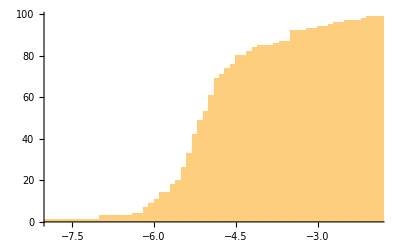

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[DecimalForm[hlist_⟦n,1⟧]]]<>","<>ToString[DecimalForm[hlist_⟦n,2⟧]]<>")",{n,1,Length[hlist]}]]
```

(-11.0784,0)(-10.0784,1)(-6.96503,2)(-6.96503,3)(-6.36756,4)(-6.1913,5)(-6.1913,6)(-6.11392,7)(-6.00623,8)(-6.00623,9)(-5.98079,10)(-5.98079,11)(-5.84064,12)(-5.8391,13)(-5.8391,14)(-5.67741,15)(-5.67741,16)(-5.65081,17)(-5.65081,18)(-5.58896,19)(-5.58896,20)(-5.45641,21)(-5.45641,22)(-5.45398,23)(-5.45398,24)(-5.40703,25)(-5.40703,26)(-5.34102,27)(-5.3148,28)(-5.3148,29)(-5.31339,30)(-5.31339,31)(-5.30381,32)(-5.30381,33)(-5.29285,34)(-5.29285,35)(-5.27271,36)(-5.23816,37)(-5.23816,38)(-5.23073,39)(-5.23073,40)(-5.22423,41)(-5.22423,42)(-5.15391,43)(-5.13491,44)(-5.13491,45)(-5.13141,46)(-5.13141,47)(-5.12727,48)(-5.12727,49)(-5.09735,50)(-5.09735,51)(-5.07799,52)(-5.07799,53)(-4.97572,54)(-4.97572,55)(-4.97496,56)(-4.93106,57)(-4.93106,58)(-4.92623,59)(-4.92623,60)(-4.92165,61)(-4.85406,62)(-4.85406,63)(-4.84778,64)(-4.84778,65)(-4.83908,66)(-4.83908,67)(-4.83751,68)(-4.83751,69)(-4.73787,70)(-4.73787,71)(-4.64736,72)(-4.64736,73)(-4.63177,74)(-4.56357,75)(-4.56357,76)(-4.4992,77)(-4.4992,78)(-4.44308,79)(-4.44308,80)(-4.21367,81)(-4.21367,82)(-4.17625,83)(-4.17625,84)(-4.04181,85)(-3.72607,86)(-3.6156,87)(-3.47511,88)(-3.47511,89)(-3.47028,90)(-3.46249,91)(-3.46249,92)(-3.15531,93)(-2.92575,94)(-2.73728,95)(-2.61462,96)(-2.4848,97)(-2.13269,98)(-2.09316,99)(-0.00000000000000201703,100)(0.5,100)

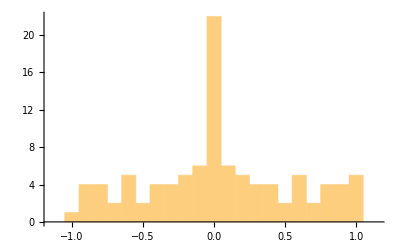

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.981357,1)(-0.946746,2)(-0.911011,3)(-0.870903,4)(-0.866445,5)(-0.815304,6)(-0.78346,7)(-0.764678,8)(-0.763745,9)(-0.706294,10)(-0.666464,11)(-0.62033,12)(-0.591897,13)(-0.586927,14)(-0.581596,15)(-0.566,16)(-0.545343,17)(-0.504679,18)(-0.447504,19)(-0.412612,20)(-0.410159,21)(-0.374031,22)(-0.345171,23)(-0.335259,24)(-0.296915,25)(-0.293144,26)(-0.24314,27)(-0.220997,28)(-0.204685,29)(-0.186744,30)(-0.164862,31)(-0.145503,32)(-0.139631,33)(-0.13292,34)(-0.0727494,35)(-0.0698716,36)(-0.0511886,37)(-0.0266491,38)(-0.0162337,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.,57)(0.0162337,58)(0.0266491,59)(0.0511886,60)(0.0698716,61)(0.0727494,62)(0.13292,63)(0.139631,64)(0.145503,65)(0.164862,66)(0.186744,67)(0.204685,68)(0.220997,69)(0.24314,70)(0.293144,71)(0.296915,72)(0.335259,73)(0.345171,74)(0.374031,75)(0.410159,76)(0.412612,77)(0.447504,78)(0.504679,79)(0.545343,80)(0.566,81)(0.581596,82)(0.586927,83)(0.591897,84)(0.62033,85)(0.666464,86)(0.706294,87)(0.763745,88)(0.764678,89)(0.78346,90)(0.815304,91)(0.866445,92)(0.870903,93)(0.911011,94)(0.946746,95)(0.981357,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

285

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersPolish=TopicClusters;
```

```mathematica
Timing[PplTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{250.969,Null}

```mathematica
Timing[PplT=Table[v=Table[prepP=PplTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.09375,Null}

```mathematica
Timing[spec=Eigenvalues[PplT];]
```

{1.60938,Null}

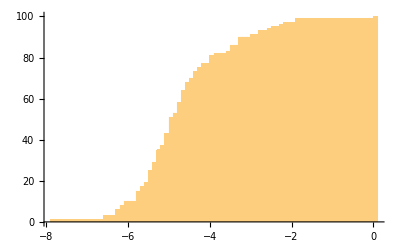

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.88047,0)(-7.88047,1)(-6.58733,2)(-6.58733,3)(-6.29415,4)(-6.29415,5)(-6.20081,6)(-6.18235,7)(-6.18235,8)(-6.06547,9)(-6.06547,10)(-5.79753,11)(-5.73872,12)(-5.73872,13)(-5.72688,14)(-5.72688,15)(-5.61625,16)(-5.61625,17)(-5.54449,18)(-5.54449,19)(-5.43803,20)(-5.43803,21)(-5.43047,22)(-5.43047,23)(-5.4078,24)(-5.4078,25)(-5.35696,26)(-5.35696,27)(-5.35202,28)(-5.35202,29)(-5.26448,30)(-5.26448,31)(-5.25312,32)(-5.25312,33)(-5.24484,34)(-5.24484,35)(-5.13375,36)(-5.13375,37)(-5.09871,38)(-5.09871,39)(-5.05044,40)(-5.05044,41)(-5.00179,42)(-5.00179,43)(-4.99235,44)(-4.99235,45)(-4.94263,46)(-4.94263,47)(-4.9289,48)(-4.9289,49)(-4.90708,50)(-4.90708,51)(-4.85078,52)(-4.85078,53)(-4.78614,54)(-4.78614,55)(-4.73703,56)(-4.70606,57)(-4.70606,58)(-4.68738,59)(-4.68738,60)(-4.6783,61)(-4.6783,62)(-4.66299,63)(-4.66299,64)(-4.53588,65)(-4.53588,66)(-4.53447,67)(-4.53447,68)(-4.42575,69)(-4.42575,70)(-4.39321,71)(-4.39321,72)(-4.35015,73)(-4.2654,74)(-4.2654,75)(-4.17903,76)(-4.17903,77)(-3.9612,78)(-3.9612,79)(-3.92207,80)(-3.92207,81)(-3.81411,82)(-3.5089,83)(-3.40748,84)(-3.40748,85)(-3.40663,86)(-3.26527,87)(-3.2017,88)(-3.2017,89)(-3.20017,90)(-2.91292,91)(-2.77444,92)(-2.77444,93)(-2.5196,94)(-2.4202,95)(-2.24289,96)(-2.11782,97)(-1.87736,98)(-1.87736,99)(0.,100)(0.5,100)

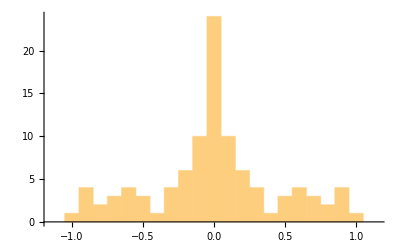

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.974702,1)(-0.913777,2)(-0.912345,3)(-0.888291,4)(-0.880731,5)(-0.843616,6)(-0.799032,7)(-0.747923,8)(-0.676398,9)(-0.66601,10)(-0.620675,11)(-0.586505,12)(-0.555107,13)(-0.552077,14)(-0.525497,15)(-0.462753,16)(-0.455991,17)(-0.400226,18)(-0.348,19)(-0.303334,20)(-0.287186,21)(-0.268336,22)(-0.232061,23)(-0.230678,24)(-0.218947,25)(-0.189943,26)(-0.168534,27)(-0.160852,28)(-0.134509,29)(-0.112216,30)(-0.111335,31)(-0.100363,32)(-0.0833855,33)(-0.0809013,34)(-0.0670178,35)(-0.0565877,36)(-0.0537169,37)(-0.0501811,38)(-0.0368382,39)(-0.0255334,40)(-0.0128529,41)(-0.00468438,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.,57)(0.,58)(0.00468438,59)(0.0128529,60)(0.0255334,61)(0.0368382,62)(0.0501811,63)(0.0537169,64)(0.0565877,65)(0.0670178,66)(0.0809013,67)(0.0833855,68)(0.100363,69)(0.111335,70)(0.112216,71)(0.134509,72)(0.160852,73)(0.168534,74)(0.189943,75)(0.218947,76)(0.230678,77)(0.232061,78)(0.268336,79)(0.287186,80)(0.303334,81)(0.348,82)(0.400226,83)(0.455991,84)(0.462753,85)(0.525497,86)(0.552077,87)(0.555107,88)(0.586505,89)(0.620675,90)(0.66601,91)(0.676398,92)(0.747923,93)(0.799032,94)(0.843616,95)(0.880731,96)(0.888291,97)(0.912345,98)(0.913777,99)(0.974702,100)(1.5,100)

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
PolishRef=TopicClustersPolish;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapPolish=StringSplit[StringReplace[ImportString[StringReplace[StringReplace[StringReplace[StringReplace[Import["Duma i uprzedzenie.txt"],{"\n":>"\n舜"}],{(s:("舜"~~Repeated[Except["\n"],{1,60}]))~~"\n":>s<>"垚"}],"":>""],{"舜":>""}],"Text"],{"垚":>"\n\n"}],"\n"~~("I"|"V"|"X"|"L")..~~"\n"];
```

```mathematica
Length[PandPChapPolish]
```

61

```mathematica
VecPolish=Table[{PolishRef_⟦k,1⟧,StringCount[PandPChapPolish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@PolishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[PolishRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecPolish,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100*√61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedPolishRef=Reverse[SortBy[Table[Cases[PolishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

87

```mathematica
Length[SiftedPolishRef]
```

86

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{62.8718,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Polish

```mathematica
ToTopicsPolish=SiftedPolishRef;
```

```mathematica
Length[ToTopicsPolish]
```

86

```mathematica
ToDeltaPolish=ReadDelta[#]&/@ToTopicsPolish;
```

```mathematica
ToNPolish=(#_⟦3⟧-1)&/@ToTopicsPolish;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersPolish,PplTopic,#_⟦1⟧&/@ToTopicsPolish];]
```

{165.823,Null}

```mathematica
ToKinPolish=KinQ;
```

```mathematica
ToEtaPolish=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsPolish,ToKinPolish}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0203012,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{brighton,26}}
0.87071327795291 | 1 | 1
{{de,39}}->{{de,37}}
0.85099936259977 | 2 | 1
{{Bourgh,35},{Bourgh's,4}}->{{bourgh,36}}
0.85110279258365 | 1 | 2
{{five,30}}->{{pięć,19},{piąte,1},{piątka,1},{piątek,1},{piątej,1},{pięcioma,1},{pięciu,8}}
0.7352947014735 | 1 | 1
{{library,23}}->{{bibliotece,9},{biblioteki,12},{bibliotekę,2},{biblioteka,1}}
0.77954617158058 | 1 | 1
{{town,64}}->{{londyn,4},{londynie,42},{londyńskim,1},{londyńskimi,1},{londynu,57}}
0.8328325494979 | 1 | 1
{{Meryton,57}}->{{meryton,54}}
0.77631536217932 | 1 | 1
{{money,26}}->{{pieniądz,1},{pieniądzach,1},{pieniądze,11},{pieniędzmi,1},{pieniędzy,14}}
0.91810042173088 | 1 | 1
{{Netherfield,73}}->{{netherfield,75}}
0.8663751735194 | 1 | 1
{{park,22}}->{{park,14},{parkiem,1},{parku,10}}
0.78862027475484 | 1 | 1
{{Pemberley,53}}->{{pemberley,60}}
0.85352315980011 | 1 | 1
{{pounds,24}}->{{funtów,27}}
0.76761494628826 | 1 | 1
{{thousand,34}}->{{tysiąc,4},{tysiące,5},{tysiąca,2},{tysiącach,1},{tysiącami,3},{tysięcy,18}}
0.89250561031148 | 1 | 1
{{Rosings,49}}->{{rosings,53}}
0.88420830108778 | 1 | 1
{{sir,78}}->{{sir,47}}
0.87605358566186 | 2 | 1
{{William,40},{William's,6}}->{{williamowi,4},{william,26},{williamem,2},{williama,14}}
0.88770965649402 | 1 | 1
{{ball,34},{balls,8}}->{{bal,19},{bale,6},{balem,3},{bali,1},{balowych,1},{balową,1},{bała,17},{balach,1},{bałam,3},{bałaś,1},{balu,22},{bały,2},{balowej,1},{balsam,1},{obalać,1},{obalić,1}}
0.77456691424387 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{katarzyną,2},{katarzynę,7},{katarzyna,88},{katarzynie,10},{katarzyno,1},{katarzyny,40}}
0.93988903092079 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotcie,5},{charlottą,8},{charlottę,9},{charlotta,47},{charlotto,4},{charlotty,19}}
0.87933582751575 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collins,118},{collinsem,6},{collinsów,4},{collinsa,41},{collinsami,1},{collinsowi,6},{collinsie,2},{collinsowie,3}}
0.91946923735704 | 1 | 1
{{colonel,65},{colonel's,1}}->{{pułkownik,45},{pułkownika,23},{pułkownikiem,3},{pułkowniku,1}}
0.88130304163444 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{darcych,4},{darcym,24},{darcy,329},{darcy♯ego,141},{darcy♯emu,18},{darcy♯go,2}}
0.91354940712763 | 1 | 1
{{dinner,33},{dinners,2}}->{{obiad,32},{obiadem,1},{obiadki,1},{obiadować,1},{obiadowała,2},{obiadowania,1},{obiadek,2},{obiadowej,1},{obiadu,3},{obiady,1},{obiadowałyśmy,1},{obiadujemy,1},{obiedzie,19}}
0.8972937019861 | 1 | 1
{{door,32},{doors,8}}->{{drzwi,24},{drzwiach,5},{drzwiczki,1},{drzwiami,2},{drzwiczkami,1}}
0.8625783071409 | 1 | 1
{{elegance,9},{elegant,14}}->{{wytworne,3},{wytwornego,2},{wytwornych,3},{wytwornym,2},{wytworną,4},{wytworna,2},{wytwornej,1},{wytworny,1},{wytworzyli,1},{wytworzyła,1},{wytwornie,1},{wytworniejszych,1},{wytworniejszym,1},{wytworniejszej,1},{wytworność,1},{wytworności,2},{wytwornością,1}}
0.84228605455184 | 1 | 1
{{estate,20},{estates,4}}->{{majątek,18},{majątkiem,2},{majętnego,1},{majętności,4},{majętnościami,1},{majątku,15}}
0.85523133863077 | 1 | 1
{{father,116},{father's,19}}->{{ojcem,10},{ojciec,76},{ojcze,2},{tatuś,16},{ojcowską,1},{ojca,56},{ojcowie,1},{tatusiu,6},{ojcu,9}}
0.8755668834199 | 1 | 1
{{Fitzwilliam,32},{Fitzwilliam's,5}}->{{fitzwilliam,11},{fitzwilliamem,1},{fitzwilliama,8},{fitzwilliamie,1}}
0.88224803672838 | 1 | 1
{{four,33},{four-and-twenty,1}}->{{czterem,1},{czterema,1},{cztery,24}}
0.88695047373326 | 1 | 1
{{girl,38},{girls,45}}->{{dziewczę,1},{dziewczęciem,2},{dziewcząt,6},{dziewczętach,1},{dziewczętom,3},{dziewczątką,1},{dziewczęta,21},{dziewczętami,3},{dziewczynki,1},{dziewczyną,1},{dziewczynę,4},{dziewczyna,7},{dziewczynek,1},{dziewczynie,3},{dziewczyno,2},{dziewczyny,4},{dziko,1}}
0.81132119187712 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,339}}
0.88955305300693 | 1 | 1
{{journey,21},{journeys,1}}->{{podróż,7},{podróżach,1},{podróże,1},{podróżować,1},{podróżą,1},{podróżowały,1},{podróżni,3},{podróżników,1},{podróżuje,1},{podróży,10}}
0.88010864571407 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitty,73}}
0.88618530791181 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lizzie,1},{lizzy,89}}
0.9154691566005 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lidii,72},{lidią,10},{lidię,14},{lidia,107},{lidio,4}}
0.86514246489844 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,38},{marii,3},{marią,3},{marię,6},{maria,8},{mariasza,1},{wymarszu,1}}
0.83953025523944 | 1 | 1
{{people,46},{people's,4}}->{{ludźmi,6},{ludzi,50},{ludziach,3},{ludzie,20},{ludziom,4}}
0.81684657185794 | 1 | 1
{{room,112},{rooms,8}}->{{pokoiki,1},{pokoiku,1},{pokoi,1},{pokój,13},{pokojach,1},{pokoje,4},{pokojem,2},{pokojów,1},{pokojówkę,2},{pokojówka,1},{pokojówkom,2},{pokoju,71}}
0.92078048741524 | 1 | 1
{{table,28},{tables,3}}->{{stół,5},{stole,9},{stołem,1},{stołowa,1},{stoliki,3},{stolika,1},{stolikach,1},{stoliku,4},{stołu,7},{stone♯a,1}}
0.73782182390011 | 1 | 1
{{week,29},{weeks,18}}->{{tydzień,14},{tygodni,14},{tygodniach,3},{tygodnie,20},{tygodnia,6},{tygodniami,1},{tygodniu,9}}
0.77211780390246 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{wickhamowi,11},{wickham,108},{wickhamem,16},{wickhamom,2},{wickhama,89},{wickhamie,12},{wickhan,1}}
0.79324922798577 | 1 | 1
{{window,16},{windows,6}}->{{oknem,1},{okna,14},{oknami,1},{oknie,4},{okno,3}}
0.76088088602008 | 1 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{cioci,7},{ciotce,7},{ciotki,20},{ciocią,1},{ciotką,4},{ciocię,2},{ciotkę,2},{ciocia,15},{ciotka,26},{ciociu,10}}
0.84670297284112 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,296},{bennetem,2},{bennetów,7},{benneta,21},{bennetowie,2}}
0.90811857018217 | 1 | 1
{{cousin,41},{cousin's,8},{cousins,11}}->{{kuzyn,8},{kuzynce,4},{kuzynki,9},{kuzynką,3},{kuzynkę,3},{kuzyna,11},{kuzynka,3},{kuzynek,2},{kuzyneczkami,1},{kuzyneczek,2},{kuzyneczko,3},{kuzyneczkom,1},{kuzyni,1},{kuzynowi,1},{kuzynie,1},{kuzynko,5},{kuzynkom,2}}
0.86872902060451 | 1 | 1
{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}}->{{elżbie,1},{elżbiecie,66},{elżbiet,1},{elżbietą,16},{elżbietę,44},{elżbieta,547},{elżbieto,28},{elżbiety,108}}
0.8296559578649 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{wieczór,25},{wieczorem,22},{wieczorów,1},{wieczora,8},{wieczorne,2},{wieczornej,2},{wieczoru,24},{wieczory,6},{wieczorze,3}}
0.8780455377668 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forster,29},{forsterem,1},{forstera,5},{forsterowi,4},{forsterowie,1}}
0.76537791018324 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,107},{gardinerem,1},{gardinera,5},{gardinerowi,1}}
0.84413854053684 | 1 | 1
{{Hurst,32},{Hurst's,1},{Hursts,1}}->{{hurst,30},{hursta,2},{hurstowi,1},{hurstowie,1}}
0.71049404386416 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{list,103},{listem,3},{listów,4},{listowego,1},{listownie,1},{listę,3},{lista,1},{listu,26},{listy,13}}
0.81309240980725 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{matki,48},{matce,9},{matką,4},{matkę,8},{mama,15},{matka,60},{mamie,3},{mamo,7},{mamusi,1},{mamusię,1},{mamusia,4},{mamusiu,1}}
0.90556968516617 | 1 | 1
{{niece,20},{niece's,2},{nieces,9}}->{{siostrzenic,2},{siostrzenicom,3},{siostrzenicą,2},{siostrzenicę,4},{siostrzenica,5},{siostrzenicy,4},{siostrzeniec,4}}
0.87187770214765 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philips,29},{philipsem,1},{philipsów,5},{philipsa,1}}
0.83107550242291 | 1 | 1
{{read,40},{reading,14},{reader,3}}->{{czytać,10},{przeczytać,5},{czyta,1},{czytaj,1},{czytają,1},{czytanie,1},{czytaniem,2},{przeczytanie,1},{czytania,3},{przeczytania,1},{przeczytaniu,1},{czytasz,1},{przeczytawszy,1},{czytelni,4},{czytelnikiem,1},{czytając,2},{czytającego,1},{czytającą,1},{czytał,5},{przeczytałem,1},{czytała,9},{przeczytała,7},{przeczytałam,1},{czytałaś,1},{przeczytałaś,1},{przeczytały,1},{czytam,1},{przeczytam,1},{czytaliśmy,1}}
0.81859839502727 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{wuj,17},{wujek,6},{wuja,23},{wujka,3},{wujaszka,2},{wujaszek,1},{wujkowi,1},{wujowi,2},{wujkiem,2},{wujowie,2},{wujostwa,10},{wujostwo,7},{wujku,2},{wuju,1}}
0.854089189943 | 1 | 1
{{wife,44},{wife's,3},{wives,1}}->{{żon,1},{żonom,1},{żoną,6},{żonę,7},{żona,15},{żono,1},{żony,26},{żonie,3}}
0.86432534657253 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingley,232},{bingleyach,1},{bingleyem,15},{bingleyów,2},{bingleya,81},{bingleyami,1},{bingleyowi,16},{bingleyu,7}}
0.9325705252067 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{brat,24},{bratem,5},{bratową,2},{brata,32},{bratowa,2},{bratanka,1},{bratowej,2},{bracie,5},{braci,1},{bratu,2}}
0.86599551261262 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{dni,38},{dzień,44},{codzienne,4},{codziennych,3},{codziennym,2},{dniach,3},{dniem,2},{dnia,64},{dniami,1},{codziennie,6},{dziennie,1},{dniu,4},{codzienny,1}}
0.75692415923932 | 1 | 1
{{dance,31},{danced,12},{dances,10},{dancing,21}}->{{tańcach,2},{tańce,13},{tańcem,3},{tańców,3},{tańczyć,7},{taniec,8},{zatańcz,1},{zatańczyć,1},{tańczą,1},{zatańczę,2},{tańca,13},{tańczących,1},{tańczącym,1},{tańczenia,2},{tańcu,3},{tańczy,2},{tańczył,9},{tańczyłby,1},{tańczyłem,1},{zatańczył,3},{tańczyła,3},{tańczyłabym,1},{tańczysz,1},{tańcujecie,1},{tańczyliśmy,1}}
0.85542047646213 | 1 | 1
{{daughter,78},{daughter's,7},{daughters,49},{daughters',1}}->{{córce,8},{córki,56},{córką,10},{córkę,17},{córka,20},{córkach,1},{córkami,2},{córek,27},{córeczko,4},{córkom,1}}
0.85990808980523 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucas,65},{lucasów,9},{lucasa,2},{lucasowie,3}}
0.88953124022155 | 1 | 1
{{plan,13},{planned,3},{planning,2},{plans,3}}->{{plan,12},{planach,5},{planem,1},{planom,3},{planów,2},{planowanego,1},{planowaną,1},{planu,4},{plany,6},{planując,1}}
0.91647110194921 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{powóz,27},{powozem,5},{powozów,2},{powozie,3},{powoziku,2},{powozu,19},{powozy,3}}
0.88137626750535 | 1 | 1
{{happily,5},{happiness,72},{happy,83},{happier,3},{happiest,10}}->{{szczęśliwe,2},{szczęśliwym,1},{szczęśliwą,3},{szczęśliwa,20},{najszczęśliwszą,4},{najszczęśliwszym,3},{szczęśliwsza,1},{szczęśliwszy,1},{szczęśliwy,10},{szczęśliwcem,1},{szczęście,38},{szczęściem,4},{szczęścia,48},{szczęściu,10},{szczęśliwej,1},{szczęśliwi,3},{szczęśliwie,7},{szczęśliwość,1},{szczęśliwości,4}}
0.88287248993866 | 1 | 1
{{invite,6},{invited,11},{inviting,3},{invitation,34},{invitations,1}}->{{zapraszać,3},{zaprasza,1},{zapraszała,5},{zapraszamy,1},{zapraszani,1},{zapraszania,1},{zapraszano,1},{zapraszany,1},{zaproszeń,3},{zaproszeni,2},{zaproszenie,29},{zaproszeniem,4},{zaproszenia,5},{zaproszeniu,4},{zaproszona,2},{zaproszono,3},{zaproszony,3},{zaprosić,2},{zaprosił,3},{zaprosili,1},{zaprosiła,5},{zaprosiły,1}}
0.88304618335432 | 1 | 1
{{knew,58},{know,238},{knowing,27},{known,57},{knows,9}}->{{wie,33},{wiem,77},{wiek,1},{wieki,4},{wiedzą,2},{wiedzę,2},{wiedząc,6},{wiedzie,1},{wiedzieć,29},{wiedział,15},{wiedziałem,9},{wiedziała,48},{wiedziałam,13},{wiedziałaś,1},{wiedziały,2},{wiedziano,3},{wiedzieli,6},{wiemy,9},{wiadome,3},{wiadomo,16},{wiadomość,29},{wiadomości,38},{wiadomościom,2},{wiadomością,7},{wiadomościami,3},{wiesz,31},{wieś,10},{wieść,5},{wieści,5},{wieku,11},{wiedzy,1},{najwięcej,6},{wiecie,1},{wioski,1},{wiodło,1},{wisiało,1},{nawiasem,1},{ponawiając,1}}
0.93084992194064 | 1 | 1
{{ladies,74},{lady,183},{lady's,8},{ladyship,30},{ladyship's,12}}->{{damskich,1},{lady,158},{damom,8},{damą,3},{damę,6},{dama,39},{damami,3},{damie,10}}
0.92837740463731 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{panną,21},{pannę,18},{panna,148},{pannami,1},{pannie,18},{panno,24},{pannom,3},{panny,82}}
0.88154292658857 | 1 | 1
{{pride,47},{prided,1},{proud,22},{proudly,1},{proudest,1}}->{{dumą,4},{dumę,3},{duma,25},{dumie,3},{dumnego,1},{dumnym,4},{dumną,2},{dumna,4},{dumnie,2},{najdumniejszym,1},{dumny,10},{dumy,7}}
0.88940576508099 | 1 | 1
{{serve,2},{serving,1},{servant,15},{servant's,2},{servants,12}}->{{służby,8},{służyć,1},{służącego,8},{służącemu,2},{służących,3},{służącą,2},{służąca,1},{służącej,1},{służący,7},{służbę,2},{służba,4}}
0.89759370797785 | 1 | 1
{{woman,55},{womanly,1},{woman's,4},{women,19},{women's,1}}->{{kobiecych,2},{kobiecym,1},{kobieca,1},{kobiecej,1},{kobiecie,1},{kobiecy,1},{kobiet,8},{kobietom,2},{kobietą,10},{kobietę,7},{kobieta,23},{kobiety,13}}
0.86398071349473 | 1 | 1
{{feel,39},{feeling,38},{feelingly,1},{feelings,86},{feels,4},{felt,100}}->{{czuje,22},{czule,2},{czułe,2},{czułego,1},{czułem,1},{czułym,1},{czują,1},{czuję,8},{czuła,35},{czułam,1},{czując,2},{uczuciu,5},{czuli,1},{czuliła,1},{czuły,1},{czułej,1},{czujesz,2},{uczuciach,2},{uczucie,33},{uczuciem,2},{uczuciom,1},{uczucia,78},{uczuciowością,1},{czułości,2},{czułością,1}}
0.82557956057601 | 1 | 1
{{marriage,66},{married,61},{marry,42},{marrying,23},{matrimonial,1},{matrimony,6}}->{{małżeństwem,2},{mężatki,1},{mężatką,2},{zamężną,3},{małżeństwa,25},{mężatka,1},{żenić,5},{małżeński,2},{małżeńskich,1},{małżeńskim,3},{ożeni,6},{ożenić,6},{poślubić,8},{ślubie,8},{małżeńskie,1},{małżeńskiego,2},{małżeństwie,11},{poślubia,1},{małżeństwo,34},{małżeństwu,3},{żonaty,2},{małżonki,3},{małżonką,1},{małżonkę,1},{małżonka,3},{małżonek,1},{poślubienia,1},{poślubiając,1},{małżeńskiej,1},{ożenił,5},{ożeniłby,1},{poślubił,8},{poślubiłby,1},{poślubiła,2},{poślubionych,1},{poślubisz,2}}
0.89837372957876 | 1 | 1
{{neighbour,8},{neighbouring,2},{neighbours,10},{neighbours',1},{neighbourhood,29},{neighbourhoods,1}}->{{sąsiad,2},{sąsiadach,1},{sąsiadki,2},{sąsiadom,2},{sąsiadów,6},{sąsiadką,1},{sąsiadkę,1},{sąsiada,2},{sąsiadka,1},{sąsiadkom,1},{sąsiedzkich,1},{sąsiedzkie,1},{sąsiednim,1},{sąsiedniego,1},{sąsiadującym,1},{sąsiedzi,3},{sąsiedztwem,1},{sąsiedztwa,2},{sąsiedztwie,9},{sąsiedztwo,8}}
0.85341691688318 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{oficer,4},{oficerach,1},{oficerem,6},{oficerom,2},{oficerów,13},{oficera,1},{oficerami,8},{oficerski,4},{oficerskich,1},{oficerskim,1},{oficerowie,5},{oficerskiego,1}}
0.85167761331031 | 1 | 1
{{visit,51},{visited,4},{visiting,5},{visits,5},{visitor,11},{visitors,14}}->{{wizycie,8},{wizyt,4},{wizytą,11},{wizytę,20},{wizyta,9},{wizytami,3},{wizyty,27},{wizytując,1}}
0.88302111392569 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{piśmie,1},{pisać,11},{pisał,8},{pisała,10},{pisałam,1},{pisałem,2},{pisały,1},{pisana,1},{pisane,2},{pisania,2},{pisanie,2},{pisaniem,1},{pisaniny,1},{pisany,5},{pisma,2},{pismem,1},{pismo,3},{pisnąć,1},{pisuj,1},{pisywać,1},{pisz,2},{piszą,1},{piszę,7},{pisząc,3},{pisze,9},{piszesz,2},{napisać,8},{napisał,3},{napisała,8},{napisałem,4},{napisania,3},{napisaniu,1},{napisz,3},{napiszę,3},{napisze,2}}
0.84036155299546 | 1 | 1
{{respect,30},{respected,3},{respectful,1},{respecting,3},{respects,6},{respectable,13},{respectability,5}}->{{szacunek,16},{szacunkiem,3},{szacunku,19},{szacownych,2},{szacownej,1},{szacujesz,1},{oszacują,1}}
0.79225859270313 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedPolishRef=Reverse[SortBy[Table[Cases[PolishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedPolishRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedPolishRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishPolish.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>Last[SortBy[ResiftedEnglishRef[[#_⟦1⟧,1]],Last]]_⟦1⟧<>"_"<>Last[SortBy[ResiftedPolishRef[[#_⟦2⟧,1]],Last]]_⟦1⟧<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

```mathematica
Export["(en)(pl).txt",StringJoin[Riffle["%"<>Last[SortBy[ResiftedEnglishRef[[#_⟦1⟧,1]],Last]]_⟦1⟧<>","<>Last[SortBy[ResiftedPolishRef[[#_⟦2⟧,1]],Last]]_⟦1⟧&/@OptimalNodes,"\n"]]]
```

(en)(pl).txt

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_Polish_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

#### Polish labels

```mathematica
FromClusters=ResiftedPolishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
PolishSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Polish"])]
```

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
PolishCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{"cz":>"ℂ","dz":>"𝔻","dź":>"ℤ","sz":>"𝕊","ch":>"𝕏","rz":>"ℝ"}]&/@w)
```

```mathematica
PolishDecompress[w_]:=StringReplace[w,{"ℂ":>"cz","𝔻":>"dz","ℤ":>"dź","𝕊":>"sz","𝕏":>"ch","ℝ":>"rz"}]
```

```mathematica
PadPrefix0[cl_]:=(HeuristicPrefixL=(Max[#]-1)&/@((Last[#]&/@StringPosition[#,WordBoundary~~AdmissiblePolishVerbPrefixes|"naj"~~LetterCharacter,Overlaps->All])&/@cl_⟦1⟧);MaxPrefixL=Max[HeuristicPrefixL];{Table[{StringDrop[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],StringPadLeft[StringTake[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],MaxPrefixL," "]},{n,1,Length[cl_⟦1⟧]}],cl_⟦2⟧})
```

```mathematica
PadPrefix[cl_]:=PolishSort[RefString=RemoveDiacritics[Last[SortBy[#_⟦1⟧&/@cl_⟦1⟧,StringLength[#]&]],Language->"Polish"];Transpose[Table[prep=SequenceAlignment[RefString,RemoveDiacritics[cl_⟦1,n,1⟧,Language->"Polish"]];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧},{cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
ClusterCount=Transpose[{{"myślicie",1},{"myśleli",1},{"umyślne",2},{"pomyśleć",1}}]
```

{{myślicie,myśleli,umyślne,pomyśleć},{1,1,2,1}}

```mathematica
EvenOut[cl_]:=(prep0=If[Or@@StringContainsQ[cl_⟦1⟧,"♯"|"mów"|"dobr"|"zobacz"|"szł"],cl,PadPrefix[PadPrefix0[cl]]];prep=PolishCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{  myśleli ,1},{  myślicie,1},{ umyślne  ,2},{pomyśleć  ,1}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,PolishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
1 | 2
 
1 | 3
m
1 | 4
y
1 | 5
ś
1 | 6
l
1 | 7
e
1 | 8
l
1 | 9
i
1 | 10
 
1
1
 
1 | 2
 
1 | 3
m
1 | 4
y
1 | 5
ś
1 | 6
l
1 | 7
i
1 | 8
c
1 | 9
i
1 | 10
e
1
1
 
2 | 2
u
2 | 3
m
2 | 4
y
2 | 5
ś
2 | 6
l
2 | 7
n
2 | 8
e
2 | 9
 
2 | 10
 
2
1
p
1 | 2
o
1 | 3
m
1 | 4
y
1 | 5
ś
1 | 6
l
1 | 7
e
1 | 8
ć
1 | 9
 
1 | 10
 
1

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{10, ,1},{10,e,1},{10, ,2},{10, ,1}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
1 | 1
 
1 | 1
 
2 | 1
p
1
2
 
1 | 2
 
1 | 2
u
2 | 2
o
1
3
myśl
5 |  |  | 
7
e
1 | 7
i
1 | 7
n
2 | 7
e
1
8
l
1 | 8
c
1 | 8
e
2 | 8
ć
1
9
i
1 | 9
i
1 | 9
 
2 | 9
 
1
10
 
1 | 10
e
1 | 10
 
2 | 10
 
1

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
p
1 | 1
 
4 |  | 
2
o
1 | 2
u
2 | 2
 
2 | 
3
myśl
5 |  |  | 
7
e
1 | 7
n
2 | 7
i
1 | 7
e
1
8
ć
1 | 8
e
2 | 8
c
1 | 8
l
1
9
 
3 | 9
i
2 |  | 
10
 
3 | 10
e
1 | 10
 
1 |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{9}, ,3,0},{{9},i,2,3}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["PolishLabels_PnP.txt",StringReplace[StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,"♯":>"'"]];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Ł":>"L","Ą":>"A","Ę":>"E"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]],{"Ż":>"\.{Z}","Ł":>"{\L}","Ę":>"\k{E}","Ą":>"\k{A}","Ć":>"\'{C}","Ś":>"\'{S}","Ń":>"\'{N}","Ź":>"\'{Z}"}]];
```

```mathematica
Export["EnglishPolish_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```